### Start choosing the example:

```mathematica
t=21;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,11,100000},{10,7,5,1000000},{10,7,9,1000000},{11,8,6,1000000},{11,8,7,1000000},{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
(*Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];*)
d2e= Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
```

Switching costs are consistent

```mathematica
(crit=CriticalCongestionSolver[d2e])//AbsoluteTiming
```

{52-u1+u5==0&&104-u3+u6==0&&52+jt10-jt17-jt18-u5+u6==0&&-jt10+jt17+jt18+u11-u5==0&&156+jt10-jt17-jt18+u12-u6==0&&jt17+jt18-jt19+jt22-jt29-jt30-jt31-u11+u12==0&&-jt10+jt19-jt22+jt29+jt30+jt31-u11+u19==0&&156+jt10-jt19+jt22-jt29-jt30-jt31-u12+u23==0&&jt29-jt32-jt33-jt34+jt36-u19+u23==0&&-jt10+jt19-jt22+jt30+jt32+jt33-jt36-jt37-u19+u24==0&&jt31+jt34+jt37-u19+u22==0&&-jt27-jt28-jt32-jt33-jt34+jt41+jt42+jt44+jt45-jt49-u23+u24==0&&156+jt10-jt19+jt22+jt27+jt28-jt30-jt31+jt36-jt41-jt42-jt44-jt45+jt49-u23+u26==0&&-jt10+jt19-jt22-jt27-jt28+jt30-jt34-jt36-jt37+jt41+jt42+jt44+jt45-jt49-u24+u28==0,jt10≥0&&0≤jt11≤104&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt36≥0&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1000≤u22≤0&&-1000≤u26≤0&&-1000≤u28≤0&&jt10+jt22≥jt19+jt32&&156+jt10+jt22+jt27+jt28≥jt19+jt29+jt30+jt31+jt41+jt42&&jt17+jt18≤52+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&jt18≤jt29+jt30+jt31&&jt18+jt28≤jt19+jt29+jt30+jt31&&156+jt10+jt16+jt28≥jt17+jt19+jt29+jt30+jt31&&156+jt10+jt16≥jt17+jt18&&jt29+jt36≥jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&jt10+jt22+jt27+jt28+jt34+jt36+jt37+jt49≤jt19+jt30+jt41+jt42+jt44+jt45&&jt10+jt22+jt27+jt28+jt33+jt34+jt36+jt37≤jt19+jt41+jt42+jt44+jt45+jt47+jt48&&jt30+jt33≥jt47+jt48+jt49,(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(jt18==jt19+jt29+jt30+jt31||jt17+jt22==0)&&(jt10+jt22==jt19||jt29+jt30+jt31==0)&&(jt27+jt28==0||156+jt10+jt22+jt27+jt28==jt19+jt29+jt30+jt31)&&(jt32+jt33+jt34==0||jt29+jt36==0)&&(jt10+jt22+jt36+jt37==jt19+jt32||jt30+jt33==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt18==jt29+jt30+jt31||jt22==0)&&(jt18+jt28==jt19+jt29+jt30+jt31||jt16==jt27)&&(156+jt10+jt16+jt28==jt17+jt19+jt29+jt30+jt31||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||jt36==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(156+jt10+jt22+jt27+jt28==jt19+jt29+jt30+jt31+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(jt29+jt36==jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(jt47+jt48+jt49==0||jt10+jt22+jt36+jt37==jt19+jt32)&&(jt31+jt34+jt37==0||u22==0)&&(156+jt10+jt22+jt27+jt28+jt36+jt49==jt19+jt30+jt31+jt41+jt42+jt44+jt45||u26==0)&&(jt10+jt22+jt27+jt28+jt34+jt36+jt37+jt49==jt19+jt30+jt41+jt42+jt44+jt45||u28==0)}

NewReduce...{jt10≥0&&0≤jt11≤104&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000≤364+8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤-3328-44 jt10+43 jt17+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤3276+52 jt10-49 jt17-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&364+4 jt10+jt27+jt28≥4 jt17+4 jt18+jt41+jt42&&jt17+jt18≤52+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&208+3 jt10+jt19≤4 jt17+3 jt18+jt22&&208+3 jt10+jt28≤4 jt17+3 jt18+jt22&&364+4 jt10+jt16+jt28≥5 jt17+4 jt18+jt22&&156+jt10+jt16≥jt17+jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48,(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(208+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(208+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||364+4 jt10+jt27+jt28==4 (jt17+jt18))&&(208+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(364+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||208+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt32+jt33+jt34==0||780+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt33==0||780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(364+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(208+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||364+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(2704+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||3328+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(35 jt10+2 (1170+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||3276+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))}

ZAnd: head is and: jt17==0||jt19==0

ReZAnd: jt17==0 (jt10==jt19||jt18==0)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt10==jt19-jt22+jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-208/3+jt18-jt19/3+jt22/3||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==jt19-jt22||jt10==-208/3+(4 jt18)/3-jt19/3+jt22/3)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18+jt29/11-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4+jt41/4+jt42/4||jt27==-jt28+jt44+jt47)&&(jt10==-65+(11 jt18)/12+jt19/12-jt22/12+jt29/12-jt33/12-jt34/12-jt37/12||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11+jt45/11||jt32==-jt33-jt34+jt41+jt48)&&(jt10==-208/3+(4 jt18)/3-jt19/3+jt22/3-jt29/3-jt30/3+jt34/3+jt37/3||jt10==-91/2+(9 jt18)/8-jt19/8+jt22/8-jt29/8-jt30/8+jt34/8+jt37/8-u1/8)&&(jt10==-1560/23+(22 jt18)/23+jt19/23-jt22/23+jt27/23+jt28/23+jt29/23+jt30/23+jt32/23+jt33/23-jt37/23-jt41/23-jt42/23-jt44/23-jt45/23||jt27==-jt28-jt32-jt33-jt34+jt41+jt44+jt47+jt48)&&(jt10==-1560/23+(22 jt18)/23+jt19/23-jt22/23+jt27/23+jt28/23+jt29/23+jt30/23+jt32/23+jt33/23-jt37/23-jt41/23-jt42/23-jt44/23-jt45/23-jt47/23-jt48/23||jt27==-jt28-jt32-jt33-jt34+jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==-1352/19+(37 jt18)/38+jt19/38-jt22/38+jt29/38+jt30/38-jt34/38-jt37/38||jt10==-832/11+(43 jt18)/44+jt19/44-jt22/44+jt29/44+jt30/44-jt34/44-jt37/44+u1/44)&&(jt10==-65+(11 jt18)/12+jt19/12-jt22/12+jt29/12-jt33/12-jt34/12-jt37/12||jt10==-1560/23+(22 jt18)/23+jt19/23-jt22/23+jt27/23+jt28/23+jt29/23+jt30/23+jt32/23+jt33/23-jt37/23-jt41/23-jt42/23-jt44/23-jt45/23-jt47/23-jt48/23)&&(jt10==-468/7+(33 jt18)/35+(2 jt19)/35-(2 jt22)/35+(2 jt29)/35+(2 jt30)/35-(2 jt34)/35-(2 jt37)/35||jt10==-63+(49 jt18)/52+(3 jt19)/52-(3 jt22)/52+(3 jt29)/52+(3 jt30)/52-(3 jt34)/52-(3 jt37)/52-u1/52) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000≤364+8 jt10-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤-3328-44 jt10+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤3276+52 jt10-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&364+4 jt10+jt27+jt28≥4 jt18+jt41+jt42&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+3 jt10+jt19≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48

ZAnd: head is and: jt10==jt19||jt18==0

ReZAnd: jt10==jt19 (jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-52+(3 jt18)/4+jt22/4||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==-52+jt18+jt22/4||jt22==0)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18+jt29/11-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4+jt41/4+jt42/4||jt27==-jt28+jt44+jt47)&&(jt10==-780/11+jt18-jt22/11+jt29/11-jt33/11-jt34/11-jt37/11||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11+jt45/11||jt32==-jt33-jt34+jt41+jt48)&&(jt10==-52+jt18+jt22/4-jt29/4-jt30/4+jt34/4+jt37/4||jt10==-364/9+jt18+jt22/9-jt29/9-jt30/9+jt34/9+jt37/9-u1/9)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt29/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22||jt27==-jt28-jt32-jt33-jt34+jt41+jt44+jt47+jt48)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt29/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22||jt27==-jt28-jt32-jt33-jt34+jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==-2704/37+jt18-jt22/37+jt29/37+jt30/37-jt34/37-jt37/37||jt10==-3328/43+jt18-jt22/43+jt29/43+jt30/43-jt34/43-jt37/43+u1/43)&&(jt10==-780/11+jt18-jt22/11+jt29/11-jt33/11-jt34/11-jt37/11||jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt29/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22)&&(jt10==-780/11+jt18-(2 jt22)/33+(2 jt29)/33+(2 jt30)/33-(2 jt34)/33-(2 jt37)/33||jt10==-468/7+jt18-(3 jt22)/49+(3 jt29)/49+(3 jt30)/49-(3 jt34)/49-(3 jt37)/49-u1/49) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt10≥0&&jt10≥jt10&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt18+jt22≥208+4 jt10+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥jt10+22 jt18+jt27+jt28+jt29+jt30+jt32+jt33&&-1000≤364+9 jt10-9 jt18-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤-3328-43 jt10+43 jt18-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤3276+49 jt10-49 jt18+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt10+jt32&&364+4 jt10+jt27+jt28≥4 jt18+jt41+jt42&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+4 jt10≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt10+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤jt10+11 jt18+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&jt10+22 jt18+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48&&jt17==0

ZAnd: head is and: jt29==0||jt32==0

ReZAnd: jt29==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-52+(3 jt18)/4+jt22/4||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==-52+jt18+jt22/4||jt22==0)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4+jt41/4+jt42/4||jt27==-jt28+jt44+jt47)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11+jt45/11||jt32==-jt33-jt34+jt41+jt48)&&(jt10==-52+jt18+jt22/4-jt30/4+jt34/4+jt37/4||jt10==-364/9+jt18+jt22/9-jt30/9+jt34/9+jt37/9-u1/9)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22||jt27==-jt28-jt32-jt33-jt34+jt41+jt44+jt47+jt48)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22||jt27==-jt28-jt32-jt33-jt34+jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==-2704/37+jt18-jt22/37+jt30/37-jt34/37-jt37/37||jt10==-3328/43+jt18-jt22/43+jt30/43-jt34/43-jt37/43+u1/43)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt41/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22)&&(jt10==-780/11+jt18-(2 jt22)/33+(2 jt30)/33-(2 jt34)/33-(2 jt37)/33||jt10==-468/7+jt18-(3 jt22)/49+(3 jt30)/49-(3 jt34)/49-(3 jt37)/49-u1/49) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt10≥0&&jt10≥jt10&&jt22≥0&&jt27≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+4 jt10+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥jt10+22 jt18+jt27+jt28+jt30+jt32+jt33&&-1000≤364+9 jt10-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328-43 jt10+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276+49 jt10-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt10+jt32&&364+4 jt10+jt27+jt28≥4 jt18+jt41+jt42&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+4 jt10≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt10+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤jt10+11 jt18+jt41+jt42+jt44+jt45+jt47+jt48&&jt10+22 jt18+jt27+jt28+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48&&jt17==0&&jt10==jt19

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-52+(3 jt18)/4+jt22/4||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==-52+jt18+jt22/4||jt22==0)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4+jt42/4||jt27==-jt28+jt44+jt47)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11+jt45/11||jt32==-jt33-jt34+jt48)&&(jt10==-52+jt18+jt22/4-jt30/4+jt34/4+jt37/4||jt10==-364/9+jt18+jt22/9-jt30/9+jt34/9+jt37/9-u1/9)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt42/22-jt44/22-jt45/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22||jt27==-jt28-jt32-jt33-jt34+jt42+jt44+jt45+jt47+jt48)&&(jt10==-2704/37+jt18-jt22/37+jt30/37-jt34/37-jt37/37||jt10==-3328/43+jt18-jt22/43+jt30/43-jt34/43-jt37/43+u1/43)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt42/22-jt44/22-jt45/22-jt47/22-jt48/22)&&(jt10==-780/11+jt18-(2 jt22)/33+(2 jt30)/33-(2 jt34)/33-(2 jt37)/33||jt10==-468/7+jt18-(3 jt22)/49+(3 jt30)/49-(3 jt34)/49-(3 jt37)/49-u1/49) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt10≥0&&jt10≥jt10&&jt22≥0&&jt27≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+4 jt10+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt42+jt44+jt45≥jt10+22 jt18+jt27+jt28+jt30+jt32+jt33&&-1000≤364+9 jt10-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328-43 jt10+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276+49 jt10-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt10+jt32&&364+4 jt10+jt27+jt28≥4 jt18+jt42&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+4 jt10≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt48&&jt27+jt28+jt32+jt33+jt34≤jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt10+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤jt10+11 jt18+jt42+jt44+jt45+jt47+jt48&&jt10+22 jt18+jt27+jt28+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt42+jt44+jt45+jt47+jt48&&jt17==0&&jt10==jt19&&jt29==0

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-52+(3 jt18)/4+jt22/4||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==-52+jt18+jt22/4||jt22==0)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28+jt44+jt47)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11+jt45/11||jt32==-jt33-jt34+jt48)&&(jt10==-52+jt18+jt22/4-jt30/4+jt34/4+jt37/4||jt10==-364/9+jt18+jt22/9-jt30/9+jt34/9+jt37/9-u1/9)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22-jt45/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22-jt45/22-jt47/22-jt48/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt45+jt47+jt48)&&(jt10==-2704/37+jt18-jt22/37+jt30/37-jt34/37-jt37/37||jt10==-3328/43+jt18-jt22/43+jt30/43-jt34/43-jt37/43+u1/43)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22-jt45/22-jt47/22-jt48/22)&&(jt10==-780/11+jt18-(2 jt22)/33+(2 jt30)/33-(2 jt34)/33-(2 jt37)/33||jt10==-468/7+jt18-(3 jt22)/49+(3 jt30)/49-(3 jt34)/49-(3 jt37)/49-u1/49) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt10≥0&&jt10≥jt10&&jt22≥0&&jt27≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+4 jt10+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt44+jt45≥jt10+22 jt18+jt27+jt28+jt30+jt32+jt33&&-1000≤364+9 jt10-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328-43 jt10+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276+49 jt10-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt10+jt32&&364+4 jt10+jt27+jt28≥4 jt18&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+4 jt10≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt48&&jt27+jt28+jt32+jt33+jt34≤jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt10+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤jt10+11 jt18+jt44+jt45+jt47+jt48&&jt10+22 jt18+jt27+jt28+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt44+jt45+jt47+jt48&&jt17==0&&jt10==jt19&&jt29==0&&jt41==0

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)&&(jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt10==-156-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt16==0)&&(jt10==-52-jt11-jt16+jt18||jt11==-jt16)&&(jt10==-52+(3 jt18)/4+jt22/4||jt22==0)&&(jt10==-208/3+jt18+jt22/3-jt28/3||jt16==jt27)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28)&&(jt10==-208/3+jt18+jt22/3||jt22==0)&&(jt10==-91-jt16/4+jt18+jt22/4-jt28/4||jt27==0)&&(jt10==-52+jt18+jt22/4||jt22==0)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt32==-jt33-jt34)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11||jt33==0)&&(jt10==-91+jt18-jt27/4-jt28/4||jt27==-jt28+jt44+jt47)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt30==-jt33)&&(jt10==-780/11+jt18-jt32/11-jt33/11-jt34/11+jt44/11||jt32==-jt33-jt34+jt48)&&(jt10==-52+jt18+jt22/4-jt30/4+jt34/4+jt37/4||jt10==-364/9+jt18+jt22/9-jt30/9+jt34/9+jt37/9-u1/9)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22-jt47/22-jt48/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt10==-2704/37+jt18-jt22/37+jt30/37-jt34/37-jt37/37||jt10==-3328/43+jt18-jt22/43+jt30/43-jt34/43-jt37/43+u1/43)&&(jt10==-780/11+jt18-jt22/11-jt33/11-jt34/11-jt37/11||jt10==-780/11+jt18-jt22/22+jt27/22+jt28/22+jt30/22+jt32/22+jt33/22-jt37/22-jt44/22-jt47/22-jt48/22)&&(jt10==-780/11+jt18-(2 jt22)/33+(2 jt30)/33-(2 jt34)/33-(2 jt37)/33||jt10==-468/7+jt18-(3 jt22)/49+(3 jt30)/49-(3 jt34)/49-(3 jt37)/49-u1/49) jt10≥0&&0≤jt11≤104&&jt16≥0&&jt18≥0&&jt10≥0&&jt10≥jt10&&jt22≥0&&jt27≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+4 jt10+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt44≥jt10+22 jt18+jt27+jt28+jt30+jt32+jt33&&-1000≤364+9 jt10-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328-43 jt10+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276+49 jt10-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt10+jt32&&364+4 jt10+jt27+jt28≥4 jt18&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208+4 jt10≤3 jt18+jt22&&208+3 jt10+jt28≤3 jt18+jt22&&364+4 jt10+jt16+jt28≥4 jt18+jt22&&156+jt10+jt16≥jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt18+jt44&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt48&&jt27+jt28+jt32+jt33+jt34≤jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt18+2 (jt10+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤jt10+11 jt18+jt44+jt47+jt48&&jt10+22 jt18+jt27+jt28+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt44+jt47+jt48&&jt17==0&&jt10==jt19&&jt29==0&&jt41==0&&jt42==0

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 (jt16==jt22+jt27||jt28==0)&&(jt22==jt32||jt30==0)&&(jt16==0||jt16==-156+jt18)&&(jt11==-52-jt16+jt18||jt16==0)&&(jt11==-jt16||jt11==-52-jt16+jt18)&&(jt18==208/3-jt22/3||jt22==0)&&(jt16==jt27||jt18==208/3-jt22/3+jt28/3)&&(jt18==91+jt27/4+jt28/4||jt27==-jt28)&&(jt18==208/3-jt22/3||jt22==0)&&(jt16==-364+4 jt18+jt22-jt28||jt27==0)&&(jt18==52-jt22/4||jt22==0)&&(jt18==780/11+jt32/11+jt33/11+jt34/11||jt32==-jt33-jt34)&&(jt18==780/11+jt32/11+jt33/11+jt34/11||jt33==0)&&(jt18==91+jt27/4+jt28/4||jt27==-jt28+jt44+jt47)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt32/11+jt33/11+jt34/11-jt44/11||jt32==-jt33-jt34+jt48)&&(jt18==52-jt22/4+jt30/4-jt34/4-jt37/4||jt18==364/9-jt22/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==780/11+jt22/22-jt27/22-jt28/22-jt30/22-jt32/22-jt33/22+jt37/22+jt44/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt18==780/11+jt22/22-jt27/22-jt28/22-jt30/22-jt32/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt27==-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt18==2704/37+jt22/37-jt30/37+jt34/37+jt37/37||jt18==3328/43+jt22/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt18==780/11+jt22/22-jt27/22-jt28/22-jt30/22-jt32/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11+(2 jt22)/33-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7+(3 jt22)/49-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) 0≤jt11≤104&&jt16≥0&&jt18≥0&&jt22≥0&&jt27≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt22+jt37+jt44≥22 jt18+jt27+jt28+jt30+jt32+jt33&&-1000≤364-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt22≥jt32&&364+jt27+jt28≥4 jt18&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt27&&jt16≤jt22+jt27&&208≤3 jt18+jt22&&208+jt28≤3 jt18+jt22&&364+jt16+jt28≥4 jt18+jt22&&156+jt16≥jt18&&780+jt32+jt33+jt34≥11 jt18+jt44&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt48&&jt27+jt28+jt32+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt22+jt34+jt37)≤33 jt18+2 jt30&&780+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+jt27+jt28+2 jt30+jt32+2 jt33≥1560+jt22+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0

ZAnd: head is and: jt16==jt22+jt27||jt28==0

ReZAnd: jt16==jt22+jt27 (jt22==jt32||jt30==0)&&(jt16==0||jt16==-156+jt18)&&(jt11==-52-jt16+jt18||jt16==0)&&(jt11==-jt16||jt11==-52-jt16+jt18)&&(jt18==208/3-jt22/3||jt22==0)&&(jt18==208/3-jt22/3+jt28/3||jt22==0)&&(jt16==jt22-jt28||jt16==-364+4 jt18+jt22-jt28)&&(jt18==208/3-jt22/3||jt22==0)&&(jt16==jt22||jt16==-364+4 jt18+jt22-jt28)&&(jt18==52-jt22/4||jt22==0)&&(jt18==780/11+jt32/11+jt33/11+jt34/11||jt32==-jt33-jt34)&&(jt18==780/11+jt32/11+jt33/11+jt34/11||jt33==0)&&(jt16==-364+4 jt18+jt22-jt28||jt16==jt22-jt28+jt44+jt47)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt32/11+jt33/11+jt34/11-jt44/11||jt32==-jt33-jt34+jt48)&&(jt18==52-jt22/4+jt30/4-jt34/4-jt37/4||jt18==364/9-jt22/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt16==1560-22 jt18+2 jt22-jt28-jt30-jt32-jt33+jt37+jt44||jt16==jt22-jt28-jt32-jt33-jt34+jt44+jt47+jt48)&&(jt16==jt22-jt28-jt32-jt33-jt34+jt44+jt47+jt48||jt16==1560-22 jt18+2 jt22-jt28-jt30-jt32-jt33+jt37+jt44+jt47+jt48)&&(jt18==2704/37+jt22/37-jt30/37+jt34/37+jt37/37||jt18==3328/43+jt22/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt16==1560-22 jt18+2 jt22-jt28-jt30-jt32-jt33+jt37+jt44+jt47+jt48||jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11)&&(jt18==780/11+(2 jt22)/33-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7+(3 jt22)/49-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) 0≤jt11≤104&&jt16≥0&&jt18≥0&&jt22≥0&&jt16-jt22≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+jt32+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt22+jt37+jt44≥jt16+22 jt18-jt22+jt28+jt30+jt32+jt33&&-1000≤364-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt22≥jt32&&364+jt16-jt22+jt28≥4 jt18&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt16-jt22&&jt16≤jt16&&208≤3 jt18+jt22&&208+jt28≤3 jt18+jt22&&364+jt16+jt28≥4 jt18+jt22&&156+jt16≥jt18&&780+jt32+jt33+jt34≥11 jt18+jt44&&jt16-jt22+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt48&&jt16-jt22+jt28+jt32+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt22+jt34+jt37)≤33 jt18+2 jt30&&780+jt16+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&jt16+22 jt18-jt22+jt28+2 jt30+jt32+2 jt33≥1560+jt22+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0

ZAnd: head is and: jt22==jt32||jt30==0

ReZAnd: jt22==jt32 (jt16==0||jt16==-156+jt18)&&(jt11==-52-jt16+jt18||jt16==0)&&(jt11==-jt16||jt11==-52-jt16+jt18)&&(jt18==208/3-jt22/3||jt22==0)&&(jt18==208/3-jt22/3+jt28/3||jt22==0)&&(jt16==jt22-jt28||jt16==-364+4 jt18+jt22-jt28)&&(jt18==208/3-jt22/3||jt22==0)&&(jt16==jt22||jt16==-364+4 jt18+jt22-jt28)&&(jt18==52-jt22/4||jt22==0)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt22==-jt33-jt34)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt33==0)&&(jt16==-364+4 jt18+jt22-jt28||jt16==jt22-jt28+jt44+jt47)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt22/11+jt33/11+jt34/11-jt44/11||jt22==-jt33-jt34+jt48)&&(jt18==52-jt22/4+jt30/4-jt34/4-jt37/4||jt18==364/9-jt22/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt16==1560-22 jt18+jt22-jt28-jt30-jt33+jt37+jt44||jt16==-jt28-jt33-jt34+jt44+jt47+jt48)&&(jt16==-jt28-jt33-jt34+jt44+jt47+jt48||jt16==1560-22 jt18+jt22-jt28-jt30-jt33+jt37+jt44+jt47+jt48)&&(jt18==2704/37+jt22/37-jt30/37+jt34/37+jt37/37||jt18==3328/43+jt22/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt16==1560-22 jt18+jt22-jt28-jt30-jt33+jt37+jt44+jt47+jt48||jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11)&&(jt18==780/11+(2 jt22)/33-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7+(3 jt22)/49-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) 0≤jt11≤104&&jt16≥0&&jt18≥0&&jt22≥0&&jt16-jt22≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+jt30&&jt22≥0&&jt33≥0&&jt34≥0&&780+jt22+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt22+jt37+jt44≥jt16+22 jt18+jt28+jt30+jt33&&-1000≤364-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt22≥jt22&&364+jt16-jt22+jt28≥4 jt18&&jt18≤52+jt11+jt16&&jt11+jt16≤jt18&&jt16≥jt16-jt22&&jt16≤jt16&&208≤3 jt18+jt22&&208+jt28≤3 jt18+jt22&&364+jt16+jt28≥4 jt18+jt22&&156+jt16≥jt18&&780+jt22+jt33+jt34≥11 jt18+jt44&&jt16-jt22+jt28≥jt44+jt47&&jt22+jt33+jt34≥jt48&&jt16+jt28+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt22+jt34+jt37)≤33 jt18+2 jt30&&780+jt16+jt22+jt28+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&jt16+22 jt18+jt28+2 jt30+2 jt33≥1560+jt22+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&jt16==jt22+jt27

ZAnd: head is and: jt16==0||jt16==-156+jt18

ReZAnd: jt16==0 (jt11==0||jt11==-52+jt18)&&(jt18==208/3-jt22/3||jt22==0)&&(jt18==208/3-jt22/3+jt28/3||jt22==0)&&(jt18==91-jt22/4+jt28/4||jt22==jt28)&&(jt18==208/3-jt22/3||jt22==0)&&(jt18==91-jt22/4+jt28/4||jt22==0)&&(jt18==52-jt22/4||jt22==0)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt22==-jt33-jt34)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt33==0)&&(jt18==91-jt22/4+jt28/4||jt22==jt28-jt44-jt47)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt22/11+jt33/11+jt34/11-jt44/11||jt22==-jt33-jt34+jt48)&&(jt18==52-jt22/4+jt30/4-jt34/4-jt37/4||jt18==364/9-jt22/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==2704/37+jt22/37-jt30/37+jt34/37+jt37/37||jt18==3328/43+jt22/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11+(2 jt22)/33-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7+(3 jt22)/49-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) 0≤jt11≤104&&jt18≥0&&jt22≥0&&-jt22≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+jt30&&jt22≥0&&jt33≥0&&jt34≥0&&780+jt22+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt22+jt37+jt44≥22 jt18+jt28+jt30+jt33&&-1000≤364-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt22≥jt22&&364-jt22+jt28≥4 jt18&&jt18≤52+jt11&&jt11≤jt18&&0≥-jt22&&208≤3 jt18+jt22&&208+jt28≤3 jt18+jt22&&364+jt28≥4 jt18+jt22&&156≥jt18&&780+jt22+jt33+jt34≥11 jt18+jt44&&-jt22+jt28≥jt44+jt47&&jt22+jt33+jt34≥jt48&&jt28+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt22+jt34+jt37)≤33 jt18+2 jt30&&780+jt22+jt28+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+jt28+2 jt30+2 jt33≥1560+jt22+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt22+jt27&&jt22==jt32

ZAnd: head is and: jt11==0||jt11==-52+jt18

ReZAnd: jt11==0 (jt18==208/3-jt22/3||jt22==0)&&(jt18==208/3-jt22/3+jt28/3||jt22==0)&&(jt18==91-jt22/4+jt28/4||jt22==jt28)&&(jt18==208/3-jt22/3||jt22==0)&&(jt18==91-jt22/4+jt28/4||jt22==0)&&(jt18==52-jt22/4||jt22==0)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt22==-jt33-jt34)&&(jt18==780/11+jt22/11+jt33/11+jt34/11||jt33==0)&&(jt18==91-jt22/4+jt28/4||jt22==jt28-jt44-jt47)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt22/11+jt33/11+jt34/11-jt44/11||jt22==-jt33-jt34+jt48)&&(jt18==52-jt22/4+jt30/4-jt34/4-jt37/4||jt18==364/9-jt22/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==2704/37+jt22/37-jt30/37+jt34/37+jt37/37||jt18==3328/43+jt22/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt22/11+jt33/11+jt34/11+jt37/11||jt18==780/11+jt22/22-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11+(2 jt22)/33-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7+(3 jt22)/49-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) jt18≥0&&jt22≥0&&-jt22≥0&&jt28≥0&&jt30≥0&&4 jt18+jt22≥208+jt30&&jt22≥0&&jt33≥0&&jt34≥0&&780+jt22+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt22+jt37+jt44≥22 jt18+jt28+jt30+jt33&&-1000≤364-9 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18-jt22+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt22-3 jt30+3 jt34+3 jt37+u1≤0&&jt22≥jt22&&364-jt22+jt28≥4 jt18&&jt18≤52&&0≤jt18&&0≥-jt22&&208≤3 jt18+jt22&&208+jt28≤3 jt18+jt22&&364+jt28≥4 jt18+jt22&&156≥jt18&&780+jt22+jt33+jt34≥11 jt18+jt44&&-jt22+jt28≥jt44+jt47&&jt22+jt33+jt34≥jt48&&jt28+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt22+jt34+jt37)≤33 jt18+2 jt30&&780+jt22+jt28+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+jt28+2 jt30+2 jt33≥1560+jt22+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt22+jt27&&jt22==jt32&&jt16==0

ZAnd: head is and: jt18==208/3-jt22/3||jt22==0

ReZAnd: jt18==208/3-jt22/3 (jt18==208/3||jt28==0)&&(jt18==208/3-jt28/3||jt18==156+jt28)&&(jt18==208/3||jt18==156+jt28)&&(jt18==0||jt18==208/3)&&(jt18==494/7+jt33/14+jt34/14||jt18==208/3+jt33/3+jt34/3)&&(jt18==494/7+jt33/14+jt34/14||jt33==0)&&(jt18==156+jt28||jt18==208/3-jt28/3+jt44/3+jt47/3)&&(jt18==494/7+jt33/14+jt34/14+jt37/14||jt30==-jt33)&&(jt18==494/7+jt33/14+jt34/14-jt44/14||jt18==208/3+jt33/3+jt34/3-jt48/3)&&(jt18==jt30-jt34-jt37||jt18==26+jt30/6-jt34/6-jt37/6+u1/6)&&(jt18==1768/25-jt28/25-jt30/25-jt33/25+jt37/25+jt44/25||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==1768/25-jt28/25-jt30/25-jt33/25+jt37/25+jt44/25+jt47/25+jt48/25||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==364/5-jt30/40+jt34/40+jt37/40||jt18==1768/23-jt30/46+jt34/46+jt37/46-u1/46)&&(jt18==494/7+jt33/14+jt34/14+jt37/14||jt18==1768/25-jt28/25-jt30/25-jt33/25+jt37/25+jt44/25+jt47/25+jt48/25)&&(jt18==212/3-(2 jt30)/39+(2 jt34)/39+(2 jt37)/39||jt18==1950/29-(3 jt30)/58+(3 jt34)/58+(3 jt37)/58+u1/58) jt18≥0&&208-3 jt18≥0&&-208+3 jt18≥0&&jt28≥0&&jt30≥0&&208+jt18≥208+jt30&&208-3 jt18≥0&&jt33≥0&&jt34≥0&&988-3 jt18+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1768-3 jt18+jt37+jt44≥22 jt18+jt28+jt30+jt33&&-1000≤156-6 jt18+jt30-jt34-jt37+u1≤0&&-1000≤-3536+46 jt18+jt30-jt34-jt37+u1≤0&&-1000≤3276+3 (208-3 jt18)-49 jt18-3 jt30+3 jt34+3 jt37+u1≤0&&208-3 jt18≥208-3 jt18&&156+3 jt18+jt28≥4 jt18&&jt18≤52&&0≤jt18&&0≥-208+3 jt18&&208+jt28≤208&&364+jt28≥208+jt18&&156≥jt18&&988-3 jt18+jt33+jt34≥11 jt18+jt44&&-208+3 jt18+jt28≥jt44+jt47&&208-3 jt18+jt33+jt34≥jt48&&jt28+jt33+jt34≤jt44+jt47+jt48&&2 (1378-3 jt18+jt34+jt37)≤33 jt18+2 jt30&&988-3 jt18+jt28+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+jt28+2 jt30+2 jt33≥1768-3 jt18+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==208-3 jt18+jt27&&208-3 jt18==jt32&&jt16==0&&jt11==0

ZAnd: head is and: jt18==208/3||jt28==0

ReZAnd: jt18==208/3 (jt28==-260/3||jt28==0)&&(jt33==-52/3-jt34||jt33==-jt34)&&(jt33==0||jt33==-52/3-jt34)&&(jt28==-260/3||jt28==jt44+jt47)&&(jt30==-jt33||jt33==-52/3-jt34-jt37)&&(jt33==-52/3-jt34+jt44||jt33==-jt34+jt48)&&(jt30==208/3+jt34+jt37||jt30==260+jt34+jt37-u1)&&(jt28==104/3-jt30-jt33+jt37+jt44||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt28==-jt33-jt34+jt44+jt47+jt48||jt28==104/3-jt30-jt33+jt37+jt44+jt47+jt48)&&(jt30==416/3+jt34+jt37||jt30==1040/3+jt34+jt37-u1)&&(jt28==104/3-jt30-jt33+jt37+jt44+jt47+jt48||jt33==-52/3-jt34-jt37)&&(jt30==26+jt34+jt37||jt30==-364/9+jt34+jt37+u1/3) False

ReZAnd: jt28==0 (jt18==208/3||jt18==156)&&(jt18==208/3||jt18==156)&&(jt18==0||jt18==208/3)&&(jt18==494/7+jt33/14+jt34/14||jt18==208/3+jt33/3+jt34/3)&&(jt18==494/7+jt33/14+jt34/14||jt33==0)&&(jt18==156||jt18==208/3+jt44/3+jt47/3)&&(jt18==494/7+jt33/14+jt34/14+jt37/14||jt30==-jt33)&&(jt18==494/7+jt33/14+jt34/14-jt44/14||jt18==208/3+jt33/3+jt34/3-jt48/3)&&(jt18==jt30-jt34-jt37||jt18==26+jt30/6-jt34/6-jt37/6+u1/6)&&(jt18==1768/25-jt30/25-jt33/25+jt37/25+jt44/25||jt33==-jt34+jt44+jt47+jt48)&&(jt18==1768/25-jt30/25-jt33/25+jt37/25+jt44/25+jt47/25+jt48/25||jt33==-jt34+jt44+jt47+jt48)&&(jt18==364/5-jt30/40+jt34/40+jt37/40||jt18==1768/23-jt30/46+jt34/46+jt37/46-u1/46)&&(jt18==494/7+jt33/14+jt34/14+jt37/14||jt18==1768/25-jt30/25-jt33/25+jt37/25+jt44/25+jt47/25+jt48/25)&&(jt18==212/3-(2 jt30)/39+(2 jt34)/39+(2 jt37)/39||jt18==1950/29-(3 jt30)/58+(3 jt34)/58+(3 jt37)/58+u1/58) jt18≥0&&208-3 jt18≥0&&-208+3 jt18≥0&&jt30≥0&&208+jt18≥208+jt30&&208-3 jt18≥0&&jt33≥0&&jt34≥0&&988-3 jt18+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1768-3 jt18+jt37+jt44≥22 jt18+jt30+jt33&&-1000≤156-6 jt18+jt30-jt34-jt37+u1≤0&&-1000≤-3536+46 jt18+jt30-jt34-jt37+u1≤0&&-1000≤3276+3 (208-3 jt18)-49 jt18-3 jt30+3 jt34+3 jt37+u1≤0&&208-3 jt18≥208-3 jt18&&156+3 jt18≥4 jt18&&jt18≤52&&0≤jt18&&0≥-208+3 jt18&&364≥208+jt18&&156≥jt18&&988-3 jt18+jt33+jt34≥11 jt18+jt44&&-208+3 jt18≥jt44+jt47&&208-3 jt18+jt33+jt34≥jt48&&jt33+jt34≤jt44+jt47+jt48&&2 (1378-3 jt18+jt34+jt37)≤33 jt18+2 jt30&&988-3 jt18+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+2 jt30+2 jt33≥1768-3 jt18+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==208-3 jt18+jt27&&208-3 jt18==jt32&&jt16==0&&jt11==0&&jt18==208/3-jt22/3

ZAnd: head is and: jt18==208/3||jt18==156

ReZAnd: jt18==208/3 (jt33==-52/3-jt34||jt33==-jt34)&&(jt33==0||jt33==-52/3-jt34)&&jt44==-jt47&&(jt30==-jt33||jt33==-52/3-jt34-jt37)&&(jt33==-52/3-jt34+jt44||jt33==-jt34+jt48)&&(jt30==208/3+jt34+jt37||jt30==260+jt34+jt37-u1)&&(jt30==104/3-jt33+jt37+jt44||jt33==-jt34+jt44+jt47+jt48)&&(jt30==104/3-jt33+jt37+jt44+jt47+jt48||jt33==-jt34+jt44+jt47+jt48)&&(jt30==416/3+jt34+jt37||jt30==1040/3+jt34+jt37-u1)&&(jt30==104/3-jt33+jt37+jt44+jt47+jt48||jt33==-52/3-jt34-jt37)&&(jt30==26+jt34+jt37||jt30==-364/9+jt34+jt37+u1/3) False

ReZAnd: jt18==156 False False

ReZAnd: jt22==0 (jt18==91+jt28/4||jt28==0)&&(jt18==780/11+jt33/11+jt34/11||jt33==-jt34)&&(jt18==780/11+jt33/11+jt34/11||jt33==0)&&(jt18==91+jt28/4||jt28==jt44+jt47)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt33/11+jt34/11-jt44/11||jt33==-jt34+jt48)&&(jt18==52+jt30/4-jt34/4-jt37/4||jt18==364/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==780/11-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==780/11-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt28==-jt33-jt34+jt44+jt47+jt48)&&(jt18==2704/37-jt30/37+jt34/37+jt37/37||jt18==3328/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt18==780/11-jt28/22-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) jt18≥0&&jt28≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&jt34≥0&&780+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt28+jt30+jt33&&-1000≤364-9 jt18+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt34+3 jt37+u1≤0&&364+jt28≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208+jt28≤3 jt18&&364+jt28≥4 jt18&&156≥jt18&&780+jt33+jt34≥11 jt18+jt44&&jt28≥jt44+jt47&&jt33+jt34≥jt48&&jt28+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt34+jt37)≤33 jt18+2 jt30&&780+jt28+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+jt28+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0

ZAnd: head is and: jt18==91+jt28/4||jt28==0

ReZAnd: jt18==91+jt28/4 (jt18==780/11+jt33/11+jt34/11||jt33==-jt34)&&(jt18==780/11+jt33/11+jt34/11||jt33==0)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt33/11+jt34/11-jt44/11||jt33==-jt34+jt48)&&(jt18==52+jt30/4-jt34/4-jt37/4||jt18==364/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26||jt18==91-jt33/4-jt34/4+jt44/4+jt47/4+jt48/4)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26||jt18==91-jt33/4-jt34/4+jt44/4+jt47/4+jt48/4)&&(jt18==2704/37-jt30/37+jt34/37+jt37/37||jt18==3328/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26)&&(jt18==780/11-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&jt34≥0&&780+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18+jt30+jt33&&-1000≤364-9 jt18+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt34+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780+jt33+jt34≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&jt33+jt34≥jt48&&-364+4 jt18+jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt34+jt37)≤33 jt18+2 jt30&&416+4 jt18+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0

ZAnd: head is and: jt18==780/11+jt33/11+jt34/11||jt33==-jt34

ReZAnd: jt18==780/11+jt33/11+jt34/11 (jt30==-jt33||jt37==0)&&(jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15+jt30/15+jt33/15-jt37/15||jt18==286/5+jt30/20+jt33/20-jt37/20+u1/20)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26+jt37/26||jt18==637/8-jt30/32-jt33/32+jt37/32-u1/32)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26||jt37==0)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11+(2 jt37)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+(3 jt37)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33-jt37+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt44+jt47+jt48&&2 (390+11 jt18-jt33+jt37)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4

ZAnd: head is and: jt30==-jt33||jt37==0

ReZAnd: jt30==-jt33 (jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==74+jt37/26+jt44/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74+jt37/26+jt44/26+jt47/26+jt48/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==74+jt37/26+jt44/26+jt47/26+jt48/26||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt44+jt47+jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11

ZAnd: head is and: jt18==780/11+jt48/11||jt44==0

ReZAnd: jt18==780/11+jt48/11 (jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15+jt37/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==1144/15+jt37/15+jt44/15+jt47/15||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-780+22 jt18+jt44+jt47&&-364+26 jt18≥780+11 jt18+jt37+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33

ZAnd: head is and: jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20

ReZAnd: jt18==988/15-jt37/15 (jt18==2912/41+jt44/41||jt18==91+jt44/4+jt47/4)&&(jt18==1066/15+jt44/30+jt47/30||jt18==91+jt44/4+jt47/4)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==1066/15+jt44/30+jt47/30)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&2548-15 jt18+jt44≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18+jt44+jt47&&-364+26 jt18≥1768-4 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==2912/41+jt44/41||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==2912/41+jt44/41 (jt18==780/11-jt47/11||jt18==2548/37-jt47/37)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==780/11-jt47/11)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-2912+41 jt18≥0&&jt47≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2912+41 jt18+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-3692+52 jt18+jt47&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-3692+63 jt18+jt47&&-364+26 jt18≥-1144+37 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15

ZAnd: head is and: jt18==780/11-jt47/11||jt18==2548/37-jt47/37

ReZAnd: jt18==780/11-jt47/11 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-2912+41 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2132+30 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2912+41 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-2912+52 jt18&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15&&jt18==2912/41+jt44/41

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-2912+41 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2132+30 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2912+41 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-2912+52 jt18&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15&&jt18==2912/41+jt44/41&&jt18==780/11-jt47/11

ReZAnd: jt18==2548/37-jt47/37 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-2912+41 jt18≥0&&2548-37 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15&&jt18==2912/41+jt44/41

$Aborted

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-2912+41 jt18≥0&&2548-37 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15&&jt18==2912/41+jt44/41&&jt18==2548/37-jt47/37

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&2548-15 jt18+jt44≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&2548-15 jt18+jt44≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15&&jt18==91+jt44/4+jt47/4

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==286/5-jt37/20+u1/20 (jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15+jt37/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==71||jt18==74+jt37/26)&&(jt18==1144/15+jt37/15+jt44/15+jt47/15||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-780+22 jt18+jt44+jt47&&-364+26 jt18≥780+11 jt18+jt37+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==74+jt37/26+jt44/26 (jt18==780/11-jt47/11||jt18==780/11+jt37/22-jt47/22)&&(jt18==71||jt18==74+jt37/26)&&(jt18==780/11-jt47/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&jt47≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18-jt37&&-364+4 jt18≥-1924+26 jt18-jt37+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2704+37 jt18-jt37+jt47&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-2704+48 jt18-jt37+jt47&&-364+26 jt18≥-1144+37 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5-jt37/20+u1/20

ZAnd: head is and: jt18==780/11-jt47/11||jt18==780/11+jt37/22-jt47/22

ReZAnd: jt18==780/11-jt47/11 (jt18==71||jt18==74+jt37/26)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18-jt37&&-364+4 jt18≥-1144+15 jt18-jt37&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1924+26 jt18-jt37&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-1924+37 jt18-jt37&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5-jt37/20+u1/20&&jt18==74+jt37/26+jt44/26

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 jt37==-19||jt37==1/2 False

ReZAnd: jt18==74+jt37/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥780-11 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤0&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1508+30 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==74+1/26 (-1924+26 jt18)+jt44/26&&jt18==780/11-jt47/11

ReZAnd: jt18==780/11+jt37/22-jt47/22 (jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&1560-22 jt18+jt37≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18-jt37&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-1144+26 jt18&&-364+26 jt18≥416+15 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5-jt37/20+u1/20&&jt18==74+jt37/26+jt44/26

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 (jt37==0||jt37==1)&&(jt37==-19||jt37==1/2) False

ReZAnd: jt18==74+jt37/26 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&-364+4 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1508+30 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==74+1/26 (-1924+26 jt18)+jt44/26&&jt18==780/11+1/22 (-1924+26 jt18)-jt47/22

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-1144+26 jt18&&-364+26 jt18≥416+15 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5-jt37/20+u1/20

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 (jt37==0||jt37==1)&&(jt37==-19||jt37==1/2) False

$Aborted

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt44==0 (jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==74+jt37/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74+jt37/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==74+jt37/26+jt47/26+jt48/26||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt47≥0&&jt48≥0&&1560+jt37≥-364+26 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt47+jt48&&-364+26 jt18≥1560+jt37+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33

ZAnd: head is and: jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20

ReZAnd: jt18==988/15-jt37/15 (jt18==2912/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41+jt47/41+jt48/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==2912/41+jt47/41+jt48/41)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt47≥0&&jt48≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18+jt47+jt48&&-364+26 jt18≥2548-15 jt18+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0

ZAnd: head is and: jt18==2912/41||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==2912/41 (jt47==-3224/41-jt48||jt47==-jt48)&&jt47==-jt48&&u1==17732/41 False

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==988/15-jt37/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1404-11 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==988/15-jt37/15&&jt18==1144/15+jt47/15+jt48/15

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==286/5-jt37/20+u1/20 (jt18==74+jt37/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74+jt37/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==71||jt18==74+jt37/26)&&(jt18==74+jt37/26+jt47/26+jt48/26||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt47≥0&&jt48≥0&&1560+jt37≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt47+jt48&&-364+26 jt18≥1560+jt37+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0

ZAnd: head is and: jt18==74+jt37/26||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==74+jt37/26 (jt18==1144/15+jt47/15+jt48/15||jt47==-jt48)&&(jt18==74||jt47==-jt48)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&jt47≥0&&jt48≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1508+30 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18+jt47+jt48&&-364+26 jt18≥-364+26 jt18+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20

ZAnd: head is and: jt18==1144/15+jt47/15+jt48/15||jt47==-jt48

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1508+30 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==74+jt37/26

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

$Aborted

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560+jt37≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&416+4 jt18-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-1144+26 jt18&&-364+26 jt18≥416+15 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==286/5-jt37/20+u1/20

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 (jt37==0||jt37==1)&&(jt37==-19||jt37==1/2) False

ReZAnd: jt18==74+jt37/26 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1508+30 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11-jt30/11+jt34/11&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==1144/15+jt47/15+jt48/15

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt37==0 (jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==74-jt30/26-jt33/26+jt44/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26+jt44/26+jt47/26+jt48/26||jt18==1144/15+jt44/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt44≥-364+26 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt44+jt47+jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11

ZAnd: head is and: jt18==780/11+jt48/11||jt44==0

ReZAnd: jt18==780/11+jt48/11 (jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==74-jt30/26-jt33/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15-jt30/15-jt33/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&1560+jt44≥-364+26 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-780+22 jt18+jt44+jt47&&-364+26 jt18+2 jt30+2 jt33≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0

ZAnd: head is and: jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20

ReZAnd: jt18==988/15+jt30/15+jt33/15 (jt18==2912/41+jt44/41||jt18==91+jt44/4+jt47/4)&&(jt18==1066/15+jt44/30+jt47/30||jt18==91+jt44/4+jt47/4)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&1560+jt44≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-780+22 jt18+jt44+jt47&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==2912/41+jt44/41||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==2912/41+jt44/41 (jt18==780/11-jt47/11||jt18==2548/37-jt47/37)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-2912+41 jt18≥0&&jt47≥0&&-780+11 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2912+41 jt18+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-3692+52 jt18+jt47&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-3692+63 jt18+jt47&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥-2132+52 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15

ZAnd: head is and: jt18==780/11-jt47/11||jt18==2548/37-jt47/37

ReZAnd: jt18==780/11-jt47/11 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-2912+41 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2132+30 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2912+41 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-2912+52 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥-1352+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15&&jt18==2912/41+jt44/41

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-2912+41 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-2132+30 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2912+41 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-2912+52 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥-1352+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15&&jt18==2912/41+jt44/41&&jt18==780/11-jt47/11

ReZAnd: jt18==2548/37-jt47/37 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-2912+41 jt18≥0&&2548-37 jt18≥0&&-780+11 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15&&jt18==2912/41+jt44/41

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-2912+41 jt18≥0&&2548-37 jt18≥0&&-780+11 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-2912+52 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15&&jt18==2912/41+jt44/41&&jt18==2548/37-jt47/37

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15&&jt18==91+jt44/4+jt47/4

ReZAnd: jt18==286/5+jt30/20+jt33/20+u1/20 (jt18==74-jt30/26-jt33/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15-jt30/15-jt33/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&jt47≥0&&-780+11 jt18≥0&&1560+jt44≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-780+11 jt18+jt44+jt47&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-780+22 jt18+jt44+jt47&&-364+26 jt18+2 jt30+2 jt33≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt18==780/11+jt48/11

$Aborted

ReZAnd: jt18==74-jt30/26-jt33/26+jt44/26 (jt18==780/11-jt47/11||jt18==780/11-jt30/22-jt33/22-jt47/22)&&(jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&-1924+26 jt18+jt30+jt33≥0&&jt47≥0&&-780+11 jt18≥0&&-364+26 jt18+jt30+jt33≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18+jt30+jt33&&-364+4 jt18≥-1924+26 jt18+jt30+jt33+jt47&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-2704+37 jt18+jt30+jt33+jt47&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-2704+48 jt18+jt30+jt33+jt47&&-364+26 jt18+2 jt30+2 jt33≥-1144+37 jt18+jt30+jt33+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+jt30/20+jt33/20+u1/20

ZAnd: head is and: jt18==780/11-jt47/11||jt18==780/11-jt30/22-jt33/22-jt47/22

ReZAnd: jt18==780/11-jt47/11 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&-1924+26 jt18+jt30+jt33≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18+jt30+jt33≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18+jt30+jt33&&-364+4 jt18≥-1144+15 jt18+jt30+jt33&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1924+26 jt18+jt30+jt33&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-1924+37 jt18+jt30+jt33&&-364+26 jt18+2 jt30+2 jt33≥-364+26 jt18+jt30+jt33&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+jt30/20+jt33/20+u1/20&&jt18==74-jt30/26-jt33/26+jt44/26

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&780-11 jt18≥0&&-780+11 jt18≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥780-11 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤0&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤11 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥1560&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==74-jt30/26+1/26 (-1924+26 jt18+jt30)+jt44/26&&jt18==780/11-jt47/11

ReZAnd: jt18==780/11-jt30/22-jt33/22-jt47/22 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&-1924+26 jt18+jt30+jt33≥0&&1560-22 jt18-jt30-jt33≥0&&-780+11 jt18≥0&&-364+26 jt18+jt30+jt33≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥-1924+37 jt18+jt30+jt33&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-1144+26 jt18&&-364+26 jt18+2 jt30+2 jt33≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+jt30/20+jt33/20+u1/20&&jt18==74-jt30/26-jt33/26+jt44/26

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&-364+4 jt18≥0&&-780+11 jt18≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==74-jt30/26+1/26 (-1924+26 jt18+jt30)+jt44/26&&jt18==780/11-jt30/22+1/22 (-1924+26 jt18+jt30)-jt47/22

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-1144+26 jt18&&-364+26 jt18+2 jt30+2 jt33≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+jt30/20+jt33/20+u1/20

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-364+4 jt18-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥1560&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-780+11 jt18≥-780+11 jt18&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==91+jt44/4+jt47/4

ReZAnd: jt44==0 (jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==74-jt30/26-jt33/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt47≥0&&jt48≥0&&1560≥-364+26 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0

ZAnd: head is and: jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20

ReZAnd: jt18==988/15+jt30/15+jt33/15 (jt18==2912/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41+jt47/41+jt48/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&jt48≥0&&1560≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤11 jt18+jt47+jt48&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt44==0

ZAnd: head is and: jt18==2912/41||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==2912/41 (jt47==-3224/41-jt48||jt47==-jt48)&&u1==17732/41 False

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==988/15+jt30/15+jt33/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (-988+15 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==988/15+jt30/15+jt33/15&&jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==286/5+jt30/20+jt33/20+u1/20 (jt18==74-jt30/26-jt33/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26-jt33/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt47≥0&&jt48≥0&&1560≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt44==0

ZAnd: head is and: jt18==74-jt30/26-jt33/26||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==74-jt30/26-jt33/26 (jt18==1144/15+jt47/15+jt48/15||jt47==-jt48)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&jt48≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥jt48&&-1144+15 jt18≤jt47+jt48&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤11 jt18+jt47+jt48&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20

ZAnd: head is and: jt18==1144/15+jt47/15+jt48/15||jt47==-jt48

ReZAnd: jt18==1144/15+jt47/15+jt48/15 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&-1144+15 jt18-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==74-jt30/26-jt33/26

ReZAnd: jt47==-jt48 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-jt47&&-1144+15 jt18≤0&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤11 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥1560&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==74-jt30/26-jt33/26

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-364+26 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&416+4 jt18+2 (-780+11 jt18-jt33)+2 jt33≤-1144+26 jt18&&-364+26 jt18+2 jt30+2 jt33≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+jt33/11+jt34/11&&jt37==0&&jt44==0&&jt18==286/5+jt30/20+jt33/20+u1/20

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt47≥0&&-1144+15 jt18-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-364+4 jt18≥jt47&&-780+11 jt18≥-1144+15 jt18-jt47&&-1144+15 jt18≤-1144+15 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&416+4 jt18+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-1144+26 jt18&&-364+26 jt18+2 (1924-26 jt18-jt30)+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt33==-jt34 (jt18==780/11||jt33==0)&&(jt18==780/11+jt37/11||jt30==-jt33)&&(jt18==780/11-jt44/11||jt48==0)&&(jt18==52+jt30/4+jt33/4-jt37/4||jt18==364/9+jt30/9+jt33/9-jt37/9+u1/9)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==2704/37-jt30/37-jt33/37+jt37/37||jt18==3328/43-jt30/43-jt33/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==74-jt30/26-jt33/26+jt37/26+jt44/26+jt47/26+jt48/26)&&(jt18==780/11-(2 jt30)/33-(2 jt33)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49-(3 jt33)/49+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-jt33≥0&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18+jt30+jt33&&-1000≤364-9 jt18+jt30+jt33-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30+jt33-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30-3 jt33+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&0≥jt48&&-364+4 jt18≤jt44+jt47+jt48&&2 (1170-jt33+jt37)≤33 jt18+2 jt30&&416+4 jt18+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4

ZAnd: head is and: jt18==780/11||jt33==0

ReZAnd: jt18==780/11 (jt30==-jt33||jt37==0)&&(jt44==0||jt48==0)&&(jt30==832/11-jt33+jt37||jt30==3016/11-jt33+jt37-u1)&&(jt30==884/11-jt33+jt37+jt44||jt44==-884/11-jt47-jt48)&&(jt30==884/11-jt33+jt37+jt44+jt47+jt48||jt44==-884/11-jt47-jt48)&&(jt30==884/11-jt33+jt37||jt30==3068/11-jt33+jt37-u1)&&(jt30==884/11-jt33+jt37+jt44+jt47+jt48||jt37==0)&&(jt30==-jt33+jt37||jt30==-728/11-jt33+jt37+u1/3) False

ReZAnd: jt33==0 (jt18==780/11+jt37/11||jt30==0)&&(jt18==780/11-jt44/11||jt48==0)&&(jt18==52+jt30/4-jt37/4||jt18==364/9+jt30/9-jt37/9+u1/9)&&(jt18==74-jt30/26+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==74-jt30/26+jt37/26+jt44/26+jt47/26+jt48/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==2704/37-jt30/37+jt37/37||jt18==3328/43-jt30/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==74-jt30/26+jt37/26+jt44/26+jt47/26+jt48/26)&&(jt18==780/11-(2 jt30)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18+jt30&&-1000≤364-9 jt18+jt30-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&0≥jt48&&-364+4 jt18≤jt44+jt47+jt48&&2 (1170+jt37)≤33 jt18+2 jt30&&416+4 jt18+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34

ZAnd: head is and: jt18==780/11+jt37/11||jt30==0

ReZAnd: jt18==780/11+jt37/11 (jt18==780/11-jt44/11||jt48==0)&&(jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20)&&(jt18==1144/15-jt30/15+jt44/15||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==1144/15-jt30/15+jt44/15+jt47/15+jt48/15||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==74-jt30/26||jt18==637/8-jt30/32-u1/32)&&(jt18==780/11-(2 jt30)/11||jt18==117/2-(3 jt30)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&jt47≥0&&jt48≥0&&780+11 jt18+jt44≥-364+26 jt18+jt30&&-1000≤1144-20 jt18+jt30+u1≤0&&-1000≤-2548+32 jt18+jt30+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 jt30+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&0≥jt48&&-364+4 jt18≤jt44+jt47+jt48&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤11 jt18+jt44+jt47+jt48&&-364+26 jt18+2 jt30≥780+11 jt18+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0

ZAnd: head is and: jt18==780/11-jt44/11||jt48==0

ReZAnd: jt18==780/11-jt44/11 (jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20)&&(jt18==74-jt30/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26||jt18==637/8-jt30/32-u1/32)&&(jt18==780/11-(2 jt30)/11||jt18==117/2-(3 jt30)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&1560≥-364+26 jt18+jt30&&-1000≤1144-20 jt18+jt30+u1≤0&&-1000≤-2548+32 jt18+jt30+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 jt30+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤780+jt47+jt48&&-364+26 jt18+2 jt30≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11

ZAnd: head is and: jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20

ReZAnd: jt18==988/15+jt30/15 (jt18==2912/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41+jt47/41+jt48/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&1560≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤780+jt47+jt48&&-364+26 jt18+2 (-988+15 jt18)≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11

ZAnd: head is and: jt18==2912/41||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==2912/41 (jt47==-3224/41-jt48||jt47==-jt48)&&u1==17732/41 False

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==988/15+jt30/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==988/15+jt30/15&&jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==286/5+jt30/20+u1/20 (jt18==74-jt30/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==74-jt30/26+jt47/26+jt48/26||jt18==1144/15+jt47/15+jt48/15)&&(jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&1560≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤780+jt47+jt48&&-364+26 jt18+2 jt30≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11

ZAnd: head is and: jt18==74-jt30/26||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==74-jt30/26 (jt18==1144/15+jt47/15+jt48/15||jt47==-jt48)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤780+jt47+jt48&&-364+2 (1924-26 jt18)+26 jt18≥1560+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20

ZAnd: head is and: jt18==1144/15+jt47/15+jt48/15||jt47==-jt48

ReZAnd: jt18==1144/15+jt47/15+jt48/15 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤-364+15 jt18&&-364+2 (1924-26 jt18)+26 jt18≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==74-jt30/26

ReZAnd: jt47==-jt48 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-jt47&&-364+4 jt18≤780-11 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤780&&-364+2 (1924-26 jt18)+26 jt18≥1560&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==74-jt30/26

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&1560≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==286/5+jt30/20+u1/20

ZAnd: head is and: jt18==71||jt18==74-jt30/26

ReZAnd: jt18==71 jt30==-1/2||jt30==19 False

ReZAnd: jt18==74-jt30/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤-364+15 jt18&&-364+2 (1924-26 jt18)+26 jt18≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt18==780/11-jt44/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt48==0 (jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20)&&(jt18==1144/15-jt30/15+jt44/15||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15-jt30/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==74-jt30/26||jt18==637/8-jt30/32-u1/32)&&(jt18==780/11-(2 jt30)/11||jt18==117/2-(3 jt30)/16+u1/16) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&jt47≥0&&780+11 jt18+jt44≥-364+26 jt18+jt30&&-1000≤1144-20 jt18+jt30+u1≤0&&-1000≤-2548+32 jt18+jt30+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 jt30+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤11 jt18+jt44+jt47&&-364+26 jt18+2 jt30≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11

ZAnd: head is and: jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20

ReZAnd: jt18==988/15+jt30/15 (jt18==1066/15+jt44/30||jt18==91+jt44/4+jt47/4)&&(jt18==1066/15+jt44/30+jt47/30||jt18==91+jt44/4+jt47/4)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&jt47≥0&&780+11 jt18+jt44≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤11 jt18+jt44+jt47&&-364+26 jt18+2 (-988+15 jt18)≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0

ZAnd: head is and: jt18==1066/15+jt44/30||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==1066/15+jt44/30 (jt18==68-jt47/26||jt47==0)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&-2132+30 jt18≥0&&jt47≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18+jt47&&-364+4 jt18≤-2132+30 jt18+jt47&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-2132+41 jt18+jt47&&-364+26 jt18+2 (-988+15 jt18)≥-1352+41 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15

ZAnd: head is and: jt18==68-jt47/26||jt47==0

ReZAnd: jt18==68-jt47/26 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&-2132+30 jt18≥0&&1768-26 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15&&jt18==1066/15+jt44/30

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&-2132+30 jt18≥0&&1768-26 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15&&jt18==1066/15+jt44/30&&jt18==68-jt47/26

ReZAnd: jt47==0 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&-2132+30 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18&&-364+4 jt18≤-2132+30 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-2132+41 jt18&&-364+26 jt18+2 (-988+15 jt18)≥-1352+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15&&jt18==1066/15+jt44/30

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&-2132+30 jt18≥0&&-1352+41 jt18≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18&&-364+4 jt18≤-2132+30 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-2132+41 jt18&&-364+26 jt18+2 (-988+15 jt18)≥-1352+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15&&jt18==1066/15+jt44/30&&jt47==0

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&780+11 jt18+jt44≥-1352+41 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&-988+15 jt18≥0&&4 jt18≥-780+15 jt18&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&780+11 jt18+jt44≥-1352+41 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18+3 (-780+11 jt18)-3 (-988+15 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 (-988+15 jt18)&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 (-988+15 jt18)≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==988/15+jt30/15&&jt18==91+jt44/4+jt47/4

ReZAnd: jt18==286/5+jt30/20+u1/20 (jt18==1144/15-jt30/15+jt44/15||jt18==91+jt44/4+jt47/4)&&(jt18==1144/15-jt30/15+jt44/15+jt47/15||jt18==91+jt44/4+jt47/4)&&(jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&jt47≥0&&780+11 jt18+jt44≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤11 jt18+jt44+jt47&&-364+26 jt18+2 jt30≥780+11 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0

ZAnd: head is and: jt18==1144/15-jt30/15+jt44/15||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==1144/15-jt30/15+jt44/15 (jt18==780/11-jt30/11-jt47/11||jt47==0)&&(jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&-1144+15 jt18+jt30≥0&&jt47≥0&&-364+26 jt18+jt30≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1144+26 jt18+jt30&&-364+4 jt18≥-1144+15 jt18+jt30+jt47&&-364+4 jt18≤-1144+15 jt18+jt30+jt47&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤-1144+26 jt18+jt30+jt47&&-364+26 jt18+2 jt30≥-364+26 jt18+jt30+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+jt30/20+u1/20

ZAnd: head is and: jt18==780/11-jt30/11-jt47/11||jt47==0

ReZAnd: jt18==780/11-jt30/11-jt47/11 (jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&-1144+15 jt18+jt30≥0&&780-11 jt18-jt30≥0&&-364+26 jt18+jt30≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1144+26 jt18+jt30&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+jt30/20+u1/20&&jt18==1144/15-jt30/15+jt44/15

ZAnd: head is and: jt18==71||jt18==74-jt30/26

ReZAnd: jt18==71 jt30==-1/2||jt30==19 False

ReZAnd: jt18==74-jt30/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&-1144+15 jt18≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤-364+15 jt18&&-364+2 (1924-26 jt18)+26 jt18≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==1144/15+1/15 (-1924+26 jt18)+jt44/15&&jt18==780/11+1/11 (-1924+26 jt18)-jt47/11

ReZAnd: jt47==0 (jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&-1144+15 jt18+jt30≥0&&-364+26 jt18+jt30≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1144+26 jt18+jt30&&-364+4 jt18≥-1144+15 jt18+jt30&&-364+4 jt18≤-1144+15 jt18+jt30&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤-1144+26 jt18+jt30&&-364+26 jt18+2 jt30≥-364+26 jt18+jt30&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+jt30/20+u1/20&&jt18==1144/15-jt30/15+jt44/15

ZAnd: head is and: jt18==71||jt18==74-jt30/26

ReZAnd: jt18==71 jt30==-1/2||jt30==19 False

ReZAnd: jt18==74-jt30/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18&&-364+4 jt18≤780-11 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤780&&-364+2 (1924-26 jt18)+26 jt18≥1560&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==1144/15+1/15 (-1924+26 jt18)+jt44/15&&jt47==0

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==71||jt18==74-jt30/26)&&(jt18==780/11-(2 jt30)/11||jt18==52+jt30) jt18≥0&&-364+4 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&780+11 jt18+jt44≥-364+26 jt18+jt30&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+3 (-780+11 jt18)-4 jt30≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤33 jt18+2 jt30&&-364+15 jt18≤-364+15 jt18&&-364+26 jt18+2 jt30≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+jt30/20+u1/20

ZAnd: head is and: jt18==71||jt18==74-jt30/26

ReZAnd: jt18==71 jt30==-1/2||jt30==19 False

ReZAnd: jt18==74-jt30/26 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&1924-26 jt18≥0&&4 jt18≥2132-26 jt18&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&780+11 jt18+jt44≥1560&&-1000≤-3692+52 jt18≤0&&-1000≤2132-4 (1924-26 jt18)-29 jt18+3 (-780+11 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (390+11 jt18)≤2 (1924-26 jt18)+33 jt18&&-364+15 jt18≤-364+15 jt18&&-364+2 (1924-26 jt18)+26 jt18≥416+15 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt18==780/11+jt37/11&&jt48==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==91+jt44/4+jt47/4

ReZAnd: jt30==0 (jt18==780/11-jt44/11||jt48==0)&&(jt18==52-jt37/4||jt18==364/9-jt37/9+u1/9)&&(jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==74+jt37/26+jt44/26+jt47/26+jt48/26||jt18==91+jt44/4+jt47/4+jt48/4)&&(jt18==2704/37+jt37/37||jt18==3328/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==74+jt37/26+jt44/26+jt47/26+jt48/26)&&(jt18==780/11+(2 jt37)/33||jt18==468/7+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤364-9 jt18-jt37+u1≤0&&-1000≤-3328+43 jt18-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&0≥jt48&&-364+4 jt18≤jt44+jt47+jt48&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤11 jt18+jt44+jt47+jt48&&-364+26 jt18≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0

ZAnd: head is and: jt18==780/11-jt44/11||jt48==0

ReZAnd: jt18==780/11-jt44/11 (jt18==52-jt37/4||jt18==364/9-jt37/9+u1/9)&&(jt18==2704/37+jt37/37||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2704/37+jt37/37+jt47/37+jt48/37||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2704/37+jt37/37||jt18==3328/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==2704/37+jt37/37+jt47/37+jt48/37)&&(jt18==780/11+(2 jt37)/33||jt18==468/7+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&2340-11 jt18+jt37≥-364+26 jt18&&-1000≤364-9 jt18-jt37+u1≤0&&-1000≤-3328+43 jt18-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤780+jt47+jt48&&-364+26 jt18≥2340-11 jt18+jt37+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0

ZAnd: head is and: jt18==52-jt37/4||jt18==364/9-jt37/9+u1/9

ReZAnd: jt18==52-jt37/4 (jt18==2912/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41+jt47/41+jt48/41||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==2912/41+jt47/41+jt48/41)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (1378-4 jt18)≤33 jt18&&624≤780+jt47+jt48&&-364+26 jt18≥2548-15 jt18+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11

ZAnd: head is and: jt18==2912/41||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==2912/41 (jt47==-3224/41-jt48||jt47==-jt48)&&jt47==-jt48&&u1==17732/41 False

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==52-jt37/4

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&2548-15 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (208-4 jt18)-96 jt18≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==52-jt37/4&&jt18==1144/15+jt47/15+jt48/15

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==364/9-jt37/9+u1/9 (jt18==2704/37+jt37/37||jt18==1144/15+jt47/15+jt48/15)&&(jt18==2704/37+jt37/37+jt47/37+jt48/37||jt18==1144/15+jt47/15+jt48/15)&&(jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/11||jt18==2704/37+jt37/37+jt47/37+jt48/37)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&2340-11 jt18+jt37≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤780+jt47+jt48&&-364+26 jt18≥2340-11 jt18+jt37+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11

ZAnd: head is and: jt18==2704/37+jt37/37||jt18==1144/15+jt47/15+jt48/15

ReZAnd: jt18==2704/37+jt37/37 (jt18==1144/15+jt47/15+jt48/15||jt47==-jt48)&&(jt18==74||jt47==-jt48)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&jt47≥0&&jt48≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥jt48&&-364+4 jt18≤780-11 jt18+jt47+jt48&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤780+jt47+jt48&&-364+26 jt18≥-364+26 jt18+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==364/9+1/9 (2704-37 jt18)+u1/9

ZAnd: head is and: jt18==1144/15+jt47/15+jt48/15||jt47==-jt48

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤-364+15 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==2704/37+jt37/37

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt47==-jt48 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-jt47&&-364+4 jt18≤780-11 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤780&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==2704/37+jt37/37

ReZAnd: jt18==1144/15+jt47/15+jt48/15 (jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/22||jt18==780/11+jt37/11)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&2340-11 jt18+jt37≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤-364+15 jt18&&-364+26 jt18≥1196+4 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==364/9-jt37/9+u1/9

ZAnd: head is and: jt18==71||jt18==2704/37+jt37/37

ReZAnd: jt18==71 (jt37==1||jt37==2)&&(jt37==-18||jt37==3/2) False

ReZAnd: jt18==2704/37+jt37/37 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&jt47≥0&&-1144+15 jt18-jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18+jt47&&0≥-1144+15 jt18-jt47&&-364+4 jt18≤-364+4 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤-364+15 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt18==780/11-jt44/11&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==1144/15+jt47/15+jt48/15

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt48==0 (jt18==52-jt37/4||jt18==364/9-jt37/9+u1/9)&&(jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==74+jt37/26+jt44/26+jt47/26||jt18==91+jt44/4+jt47/4)&&(jt18==2704/37+jt37/37||jt18==3328/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==74+jt37/26+jt44/26+jt47/26)&&(jt18==780/11+(2 jt37)/33||jt18==468/7+(3 jt37)/49+u1/49) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤364-9 jt18-jt37+u1≤0&&-1000≤-3328+43 jt18-jt37+u1≤0&&-1000≤3276-49 jt18+3 jt37+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤11 jt18+jt44+jt47&&-364+26 jt18≥1560+jt37+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0

ZAnd: head is and: jt18==52-jt37/4||jt18==364/9-jt37/9+u1/9

ReZAnd: jt18==52-jt37/4 (jt18==1066/15+jt44/30||jt18==91+jt44/4+jt47/4)&&(jt18==1066/15+jt44/30+jt47/30||jt18==91+jt44/4+jt47/4)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==1066/15+jt44/30+jt47/30)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&jt44≥0&&jt47≥0&&1768-4 jt18+jt44≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (1378-4 jt18)≤33 jt18&&624≤11 jt18+jt44+jt47&&-364+26 jt18≥1768-4 jt18+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0

ZAnd: head is and: jt18==1066/15+jt44/30||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==1066/15+jt44/30 (jt18==68-jt47/26||jt47==0)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt47==0)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&-2132+30 jt18≥0&&jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18+jt47&&-364+4 jt18≤-2132+30 jt18+jt47&&2 (1378-4 jt18)≤33 jt18&&624≤-2132+41 jt18+jt47&&-364+26 jt18≥-364+26 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4

ZAnd: head is and: jt18==68-jt47/26||jt47==0

ReZAnd: jt18==68-jt47/26 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&-2132+30 jt18≥0&&1768-26 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4&&jt18==1066/15+jt44/30

$Aborted

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&-2132+30 jt18≥0&&1768-26 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (208-4 jt18)-96 jt18≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4&&jt18==1066/15+jt44/30&&jt18==68-jt47/26

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt47==0 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&-2132+30 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18&&-364+4 jt18≤-2132+30 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-2132+41 jt18&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4&&jt18==1066/15+jt44/30

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&-2132+30 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (208-4 jt18)-96 jt18≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-2132+41 jt18&&-364+4 jt18≥-2132+30 jt18&&-364+4 jt18≤-2132+30 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-2132+41 jt18&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4&&jt18==1066/15+jt44/30&&jt47==0

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&1768-4 jt18+jt44≥-364+26 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (208-4 jt18)-49 jt18+u1≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&208-4 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&1768-4 jt18+jt44≥-364+26 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (208-4 jt18)-96 jt18≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1378-4 jt18)≤33 jt18&&624≤-364+15 jt18&&-364+26 jt18≥1404&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==52-jt37/4&&jt18==91+jt44/4+jt47/4

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==364/9-jt37/9+u1/9 (jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4)&&(jt18==74+jt37/26+jt44/26+jt47/26||jt18==91+jt44/4+jt47/4)&&(jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/11||jt18==74+jt37/26+jt44/26+jt47/26)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥jt44+jt47&&-364+4 jt18≤jt44+jt47&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤11 jt18+jt44+jt47&&-364+26 jt18≥1560+jt37+jt44+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0

ZAnd: head is and: jt18==74+jt37/26+jt44/26||jt18==91+jt44/4+jt47/4

ReZAnd: jt18==74+jt37/26+jt44/26 (jt18==780/11+jt37/22-jt47/22||jt47==0)&&(jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/11||jt47==0)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&jt47≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1924+37 jt18-jt37&&-364+4 jt18≥-1924+26 jt18-jt37+jt47&&-364+4 jt18≤-1924+26 jt18-jt37+jt47&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤-1924+37 jt18-jt37+jt47&&-364+26 jt18≥-364+26 jt18+jt47&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9-jt37/9+u1/9

ZAnd: head is and: jt18==780/11+jt37/22-jt47/22||jt47==0

ReZAnd: jt18==780/11+jt37/22-jt47/22 (jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/22||jt18==780/11+jt37/11)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&1560-22 jt18+jt37≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1924+37 jt18-jt37&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤-364+15 jt18&&-364+26 jt18≥1196+4 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9-jt37/9+u1/9&&jt18==74+jt37/26+jt44/26

ZAnd: head is and: jt18==71||jt18==2704/37+jt37/37

ReZAnd: jt18==71 (jt37==1||jt37==2)&&(jt37==-18||jt37==3/2) False

ReZAnd: jt18==2704/37+jt37/37 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&-1144+15 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤-364+15 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==74+1/26 (-2704+37 jt18)+jt44/26&&jt18==780/11+1/22 (-2704+37 jt18)-jt47/22

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt47==0 (jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&-1924+26 jt18-jt37≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥-1924+37 jt18-jt37&&-364+4 jt18≥-1924+26 jt18-jt37&&-364+4 jt18≤-1924+26 jt18-jt37&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤-1924+37 jt18-jt37&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9-jt37/9+u1/9&&jt18==74+jt37/26+jt44/26

$Aborted

ReZAnd: jt18==71 jt37==-18||jt37==3/2 False

ReZAnd: jt18==2704/37+jt37/37 jt18==1976/27||jt18==3068/41 jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&780-11 jt18≥0&&-364+26 jt18≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&-364+4 jt18≥780-11 jt18&&-364+4 jt18≤780-11 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤780&&-364+26 jt18≥-364+26 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==74+1/26 (-2704+37 jt18)+jt44/26&&jt47==0

ReZAnd: jt18==91+jt44/4+jt47/4 (jt18==71||jt18==2704/37+jt37/37)&&(jt18==780/11+jt37/22||jt18==780/11+jt37/11)&&(jt18==780/11+(2 jt37)/33||jt18==364/5+jt37/10) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&jt37≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&1560+jt37+jt44≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 jt37≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (1170+jt37)≤33 jt18&&416+4 jt18+jt37≤-364+15 jt18&&-364+26 jt18≥1196+4 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9-jt37/9+u1/9

ZAnd: head is and: jt18==71||jt18==2704/37+jt37/37

ReZAnd: jt18==71 (jt37==1||jt37==2)&&(jt37==-18||jt37==3/2) False

ReZAnd: jt18==2704/37+jt37/37 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&-364+4 jt18≥0&&4 jt18≥208&&780≥11 jt18&&-2704+37 jt18≥0&&jt44≥0&&-364+4 jt18-jt44≥0&&-1144+37 jt18+jt44≥-364+26 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2912-40 jt18+4 (-2704+37 jt18)≤0&&4 jt18≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&-156+4 jt18≤3 jt18&&4 jt18≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&-364+4 jt18≥-364+4 jt18&&-364+4 jt18≤-364+4 jt18&&2 (-1534+37 jt18)≤33 jt18&&-2288+41 jt18≤-364+15 jt18&&-364+26 jt18≥-1508+41 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt18==91+jt28/4&&0==-jt34&&jt33==0&&jt30==0&&jt48==0&&jt18==364/9+1/9 (2704-37 jt18)+u1/9&&jt18==91+jt44/4+jt47/4

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt28==0 (jt18==780/11+jt33/11+jt34/11||jt33==-jt34)&&(jt18==780/11+jt33/11+jt34/11||jt33==0)&&(jt18==91||jt44==-jt47)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt30==-jt33)&&(jt18==780/11+jt33/11+jt34/11-jt44/11||jt33==-jt34+jt48)&&(jt18==52+jt30/4-jt34/4-jt37/4||jt18==364/9+jt30/9-jt34/9-jt37/9+u1/9)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22||jt33==-jt34+jt44+jt47+jt48)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt33==-jt34+jt44+jt47+jt48)&&(jt18==2704/37-jt30/37+jt34/37+jt37/37||jt18==3328/43-jt30/43+jt34/43+jt37/43-u1/43)&&(jt18==780/11+jt33/11+jt34/11+jt37/11||jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11-(2 jt30)/33+(2 jt34)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt34)/49+(3 jt37)/49+u1/49) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&jt34≥0&&780+jt33+jt34≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30+jt33&&-1000≤364-9 jt18+jt30-jt34-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt34-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt34+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&780+jt33+jt34≥11 jt18+jt44&&0≥jt44+jt47&&jt33+jt34≥jt48&&jt33+jt34≤jt44+jt47+jt48&&2 (1170+jt34+jt37)≤33 jt18+2 jt30&&780+2 jt33+2 jt34+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0

ZAnd: head is and: jt18==780/11+jt33/11+jt34/11||jt33==-jt34

ReZAnd: jt18==780/11+jt33/11+jt34/11 (jt18==91||jt44==-jt47)&&(jt30==-jt33||jt37==0)&&(jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15+jt30/15+jt33/15-jt37/15||jt18==286/5+jt30/20+jt33/20-jt37/20+u1/20)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22||jt18==780/11+jt44/11+jt47/11+jt48/11)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt18==780/11+jt44/11+jt47/11+jt48/11)&&(jt18==74-jt30/26-jt33/26+jt37/26||jt18==637/8-jt30/32-jt33/32+jt37/32-u1/32)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt37==0)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11+(2 jt37)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+(3 jt37)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33-jt37+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&0≥jt44+jt47&&-780+11 jt18≥jt48&&-780+11 jt18≤jt44+jt47+jt48&&2 (390+11 jt18-jt33+jt37)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0

ZAnd: head is and: jt18==91||jt44==-jt47

ReZAnd: jt18==91 (jt30==-jt33||jt37==0)&&(jt44==0||jt48==221)&&(jt30==377-jt33+jt37||jt30==676-jt33+jt37-u1)&&(jt30==-442-jt33+jt37+jt44||jt44==221-jt47-jt48)&&(jt30==-442-jt33+jt37+jt44+jt47+jt48||jt44==221-jt47-jt48)&&(jt30==-442-jt33+jt37||jt30==-364-jt33+jt37-u1)&&(jt30==-442-jt33+jt37+jt44+jt47+jt48||jt37==0)&&(jt30==-221/2-jt33+jt37||jt30==-520/3-jt33+jt37+u1/3) False

ReZAnd: jt44==-jt47 (jt30==-jt33||jt37==0)&&(jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15+jt30/15+jt33/15-jt37/15||jt18==286/5+jt30/20+jt33/20-jt37/20+u1/20)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22||jt18==780/11+jt48/11)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==74-jt30/26-jt33/26+jt37/26||jt18==637/8-jt30/32-jt33/32+jt37/32-u1/32)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt48/22||jt37==0)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11+(2 jt37)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+(3 jt37)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&-jt44≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33-jt37+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18-jt33+jt37)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33+jt37≤11 jt18+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt37+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11

ZAnd: head is and: jt30==-jt33||jt37==0

ReZAnd: jt30==-jt33 (jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==780/11+jt37/22+jt44/22||jt18==780/11+jt48/11)&&(jt18==780/11+jt37/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==780/11+jt37/22+jt48/22||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&-jt44≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt48&&22 jt18≥1560+jt37+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47

ZAnd: head is and: jt18==780/11+jt48/11||jt44==0

ReZAnd: jt18==780/11+jt48/11 (jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt37+jt44≥22 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-780+22 jt18&&22 jt18≥780+11 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47&&jt30==-jt33

ZAnd: head is and: jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20

ReZAnd: jt18==988/15-jt37/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&2548-15 jt18+jt44≥22 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1768-15 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥1768-4 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47&&jt30==-jt33&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

$Aborted

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&2548-15 jt18+jt44≥22 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1768-15 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥1768-4 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==988/15-jt37/15

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==286/5-jt37/20+u1/20 (jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt37+jt44≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-780+22 jt18&&22 jt18≥780+11 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47&&jt30==-jt33&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 (jt37==0||jt37==1)&&(jt37==-19||jt37==1/2) False

ReZAnd: jt18==74+jt37/26 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&-364+26 jt18+jt44≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1144+26 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥-1144+37 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&jt44==-jt47&&jt30==-jt33&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18)+u1/20

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt44==0 (jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20)&&(jt18==780/11+jt37/22||jt18==780/11+jt48/11)&&(jt18==780/11+jt37/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==74+jt37/26||jt18==637/8+jt37/32-u1/32)&&(jt18==780/11+jt37/22+jt48/22||jt37==0)&&(jt18==780/11+(2 jt37)/11||jt18==117/2+(3 jt37)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt48≥0&&1560+jt37≥22 jt18&&-1000≤1144-20 jt18-jt37+u1≤0&&-1000≤-2548+32 jt18-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt48&&22 jt18≥1560+jt37+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33

ZAnd: head is and: jt18==988/15-jt37/15||jt18==286/5-jt37/20+u1/20

ReZAnd: jt18==988/15-jt37/15 (jt18==2548/37||jt18==780/11+jt48/11)&&(jt18==2548/37+jt48/37||jt18==780/11+jt48/11)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==2548/37+jt48/37)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&jt48≥0&&2548-15 jt18≥22 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1768-15 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18+jt48&&22 jt18≥2548-15 jt18+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0

ZAnd: head is and: jt18==2548/37||jt18==780/11+jt48/11

ReZAnd: jt18==2548/37 (jt48==-832/37||jt48==0)&&u1==11076/37&&jt48==0&&u1==11128/37 False

ReZAnd: jt18==780/11+jt48/11 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-780+11 jt18≥0&&2548-15 jt18≥22 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276+3 (988-15 jt18)-49 jt18-3 jt30+3 (-780+11 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1768-15 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥1768-4 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==988/15-jt37/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 False False

ReZAnd: jt18==3536/47-u1/47 (jt18==988/15||jt18==68)&&(jt18==2756/41||jt18==1859/27) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&988-15 jt18≥0&&-780+11 jt18≥0&&2548-15 jt18≥22 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812+3 (988-15 jt18)-96 jt18-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&1768-15 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥1768-4 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==988/15-jt37/15&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==988/15||jt18==68

ReZAnd: jt18==988/15 False False

ReZAnd: jt18==68 False False

ReZAnd: jt18==286/5-jt37/20+u1/20 (jt18==780/11+jt37/22||jt18==780/11+jt48/11)&&(jt18==780/11+jt37/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/22+jt48/22||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&jt48≥0&&1560+jt37≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤11 jt18+jt48&&22 jt18≥1560+jt37+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0

ZAnd: head is and: jt18==780/11+jt37/22||jt18==780/11+jt48/11

ReZAnd: jt18==780/11+jt37/22 (jt18==780/11+jt48/11||jt48==0)&&(jt18==71||jt18==91)&&(jt18==780/11||jt48==0)&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1560+22 jt18≥0&&jt48≥0&&22 jt18≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1560+22 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&-780+22 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18+jt48&&22 jt18≥22 jt18+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18)+u1/20

ZAnd: head is and: jt18==780/11+jt48/11||jt48==0

ReZAnd: jt18==780/11+jt48/11 (jt18==71||jt18==91)&&jt18==780/11&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1560+22 jt18≥0&&-780+11 jt18≥0&&22 jt18≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1560+22 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&-780+22 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥-780+33 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18)+u1/20&&jt18==780/11+jt37/22

ZAnd: head is and: jt18==71||jt18==91

$Aborted

ReZAnd: jt18==91 False False

ReZAnd: jt48==0 (jt18==71||jt18==91)&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1560+22 jt18≥0&&22 jt18≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1560+22 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥0&&-780+11 jt18≤0&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&-780+22 jt18-2 jt30+2 (-780+11 jt18+jt30)≤11 jt18&&22 jt18≥22 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18)+u1/20&&jt18==780/11+jt37/22

ZAnd: head is and: jt18==71||jt18==91

ReZAnd: jt18==71 False False

ReZAnd: jt18==91 False False

ReZAnd: jt18==780/11+jt48/11 (jt18==71||jt18==74+jt37/26)&&(jt18==780/11+jt37/11||jt37==0)&&(jt18==52-jt37||jt18==780/11+(2 jt37)/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&jt37≥0&&-780+11 jt18≥0&&1560+jt37≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-3 jt30+3 (-780+11 jt18+jt30)+4 jt37≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18+jt30+jt37)≤33 jt18+2 jt30&&780-2 jt30+2 (-780+11 jt18+jt30)+jt37≤-780+22 jt18&&22 jt18≥780+11 jt18+jt37&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==286/5-jt37/20+u1/20

ZAnd: head is and: jt18==71||jt18==74+jt37/26

ReZAnd: jt18==71 (jt37==0||jt37==1)&&(jt37==-19||jt37==1/2) False

ReZAnd: jt18==74+jt37/26 (jt18==74||jt18==1144/15)&&(jt18==1976/27||jt18==3068/41) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-jt30≥0&&-780+11 jt18+jt30≥0&&11 jt18≥11 jt18&&-1924+26 jt18≥0&&-780+11 jt18≥0&&-364+26 jt18≥22 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18+4 (-1924+26 jt18)-3 jt30+3 (-780+11 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&-1144+26 jt18-2 jt30+2 (-780+11 jt18+jt30)≤-780+22 jt18&&22 jt18≥-1144+37 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11-jt30/11+jt34/11&&0==-jt47&&jt30==-jt33&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18)+u1/20&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==74||jt18==1144/15

ReZAnd: jt18==74 False False

ReZAnd: jt18==1144/15 False False

ReZAnd: jt37==0 (jt18==780/11+jt48/11||jt44==0)&&(jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==780/11-jt30/22-jt33/22+jt44/22||jt18==780/11+jt48/11)&&(jt18==780/11-jt30/22-jt33/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&jt48≥0&&1560+jt44≥22 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&jt44==-jt47

ZAnd: head is and: jt18==780/11+jt48/11||jt44==0

ReZAnd: jt18==780/11+jt48/11 (jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥22 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤-780+22 jt18&&22 jt18+2 jt30+2 jt33≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&jt44==-jt47&&jt37==0

ZAnd: head is and: jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20

ReZAnd: jt18==988/15+jt30/15+jt33/15 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥-988+37 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&780+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (-988+15 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt44==-jt47&&jt37==0&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥-988+37 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&780+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (-988+15 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&jt44==-jt47&&jt37==0&&jt18==780/11+jt48/11&&jt18==988/15+jt30/15+jt33/15

ReZAnd: jt18==286/5+jt30/20+jt33/20+u1/20 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥22 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤-780+22 jt18&&22 jt18+2 jt30+2 jt33≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&jt44==-jt47&&jt37==0&&jt18==780/11+jt48/11

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&jt44≥0&&-jt44≥0&&-780+11 jt18≥0&&1560+jt44≥1924-4 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18+jt44&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&780+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (1924-26 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&jt44==-jt47&&jt37==0&&jt18==780/11+jt48/11&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20

ReZAnd: jt44==0 (jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20)&&(jt18==780/11-jt30/22-jt33/22||jt18==780/11+jt48/11)&&(jt18==780/11-jt30/22-jt33/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==74-jt30/26-jt33/26||jt18==637/8-jt30/32-jt33/32-u1/32)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==117/2-(3 jt30)/16-(3 jt33)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt48≥0&&1560≥22 jt18+jt30+jt33&&-1000≤1144-20 jt18+jt30+jt33+u1≤0&&-1000≤-2548+32 jt18+jt30+jt33+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (-780+11 jt18-jt33)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&0==-jt47&&jt37==0

ZAnd: head is and: jt18==988/15+jt30/15+jt33/15||jt18==286/5+jt30/20+jt33/20+u1/20

ReZAnd: jt18==988/15+jt30/15+jt33/15 (jt18==2548/37||jt18==780/11+jt48/11)&&(jt18==2548/37+jt48/37||jt18==780/11+jt48/11)&&(jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&jt48≥0&&1560≥-988+37 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&780+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤11 jt18+jt48&&22 jt18+2 (-988+15 jt18-jt30)+2 jt30≥1560+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0

ZAnd: head is and: jt18==2548/37||jt18==780/11+jt48/11

ReZAnd: jt18==2548/37 (jt48==-832/37||jt48==0)&&u1==11076/37&&u1==11128/37 False

ReZAnd: jt18==780/11+jt48/11 (jt18==2912/41||jt18==3536/47-u1/47)&&(jt18==2756/41||jt18==3900/61+u1/61) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-780+11 jt18≥0&&1560≥-988+37 jt18&&-1000≤156-5 jt18+u1≤0&&-1000≤-3536+47 jt18+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 (208-4 jt18+jt30)+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&780+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (-988+15 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==988/15+jt30/15+jt33/15

ZAnd: head is and: jt18==2912/41||jt18==3536/47-u1/47

ReZAnd: jt18==2912/41 u1==17732/41 False

ReZAnd: jt18==3536/47-u1/47 jt18==2756/41||jt18==1859/27 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&-988+15 jt18-jt30≥0&&208-4 jt18+jt30≥0&&11 jt18≥11 jt18&&-780+11 jt18≥0&&1560≥-988+37 jt18&&-1000≤3692-52 jt18≤0&&-1000≤6812-96 jt18-3 jt30+3 (208-4 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (1378-4 jt18+jt30)≤33 jt18+2 jt30&&780+2 (-988+15 jt18-jt30)+2 (208-4 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (-988+15 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (-988+15 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==988/15+jt30/15+jt33/15&&jt18==780/11+jt48/11

ReZAnd: jt18==286/5+jt30/20+jt33/20+u1/20 (jt18==780/11-jt30/22-jt33/22||jt18==780/11+jt48/11)&&(jt18==780/11-jt30/22-jt33/22+jt48/22||jt18==780/11+jt48/11)&&(jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&jt48≥0&&1560≥22 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤11 jt18+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&0==-jt47&&jt37==0&&jt44==0

ZAnd: head is and: jt18==780/11-jt30/22-jt33/22||jt18==780/11+jt48/11

ReZAnd: jt18==780/11-jt30/22-jt33/22 (jt18==780/11+jt48/11||jt48==0)&&(jt18==71||jt18==91)&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1560-22 jt18-jt30≥0&&-2340+33 jt18+jt30≥0&&11 jt18≥11 jt18&&jt48≥0&&-1000≤-3692+52 jt18≤0&&-1000≤572-7 jt18-3 jt30+3 (-2340+33 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥jt48&&-780+11 jt18≤jt48&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&780+2 (1560-22 jt18-jt30)+2 (-2340+33 jt18+jt30)≤11 jt18+jt48&&22 jt18+2 (1560-22 jt18-jt30)+2 jt30≥1560+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (1560-22 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18-jt30)+jt30/20+u1/20

ZAnd: head is and: jt18==780/11+jt48/11||jt48==0

ReZAnd: jt18==780/11+jt48/11 (jt18==71||jt18==91)&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1560-22 jt18-jt30≥0&&-2340+33 jt18+jt30≥0&&11 jt18≥11 jt18&&-780+11 jt18≥0&&-1000≤-3692+52 jt18≤0&&-1000≤572-7 jt18-3 jt30+3 (-2340+33 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&780+2 (1560-22 jt18-jt30)+2 (-2340+33 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (1560-22 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (1560-22 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18-jt30)+jt30/20+u1/20&&jt18==780/11-jt30/22-jt33/22

ZAnd: head is and: jt18==71||jt18==91

ReZAnd: jt18==71 False False

ReZAnd: jt18==91 False False

ReZAnd: jt48==0 (jt18==71||jt18==91)&&(jt18==1612/23||jt18==780/11) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1560-22 jt18-jt30≥0&&-2340+33 jt18+jt30≥0&&11 jt18≥11 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤572-7 jt18-3 jt30+3 (-2340+33 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥0&&-780+11 jt18≤0&&2 (-1170+33 jt18+jt30)≤33 jt18+2 jt30&&780+2 (1560-22 jt18-jt30)+2 (-2340+33 jt18+jt30)≤11 jt18&&22 jt18+2 (1560-22 jt18-jt30)+2 jt30≥1560&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (1560-22 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1560-22 jt18-jt30)+jt30/20+u1/20&&jt18==780/11-jt30/22-jt33/22

ZAnd: head is and: jt18==71||jt18==91

ReZAnd: jt18==71 False False

ReZAnd: jt18==91 False False

ReZAnd: jt18==780/11+jt48/11 (jt18==71||jt18==74-jt30/26-jt33/26)&&(jt18==780/11-(2 jt30)/11-(2 jt33)/11||jt18==52+jt30+jt33) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-780+11 jt18-jt33≥0&&11 jt18≥11 jt18&&-780+11 jt18≥0&&1560≥22 jt18+jt30+jt33&&-1000≤-3692+52 jt18≤0&&-1000≤2132-29 jt18-4 jt30+3 (-780+11 jt18-jt33)-jt33≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (390+11 jt18-jt33)≤33 jt18+2 jt30&&780+2 (-780+11 jt18-jt33)+2 jt33≤-780+22 jt18&&22 jt18+2 jt30+2 jt33≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+jt33/11+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==286/5+jt30/20+jt33/20+u1/20

ZAnd: head is and: jt18==71||jt18==74-jt30/26-jt33/26

ReZAnd: jt18==71 jt30==-1/2-jt33||jt30==19-jt33 False

ReZAnd: jt18==74-jt30/26-jt33/26 jt18==1976/27||jt18==3068/41 jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&1924-26 jt18-jt30≥0&&-2704+37 jt18+jt30≥0&&11 jt18≥11 jt18&&-780+11 jt18≥0&&1560≥1924-4 jt18&&-1000≤-3692+52 jt18≤0&&-1000≤208-3 jt18-3 jt30+3 (-2704+37 jt18+jt30)≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&11 jt18≥11 jt18&&-780+11 jt18≥-780+11 jt18&&-780+11 jt18≤-780+11 jt18&&2 (-1534+37 jt18+jt30)≤33 jt18+2 jt30&&780+2 (1924-26 jt18-jt30)+2 (-2704+37 jt18+jt30)≤-780+22 jt18&&22 jt18+2 (1924-26 jt18-jt30)+2 jt30≥780+11 jt18&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&jt18==780/11+1/11 (1924-26 jt18-jt30)+jt34/11&&0==-jt47&&jt37==0&&jt44==0&&jt18==286/5+1/20 (1924-26 jt18-jt30)+jt30/20+u1/20&&jt18==780/11+jt48/11

ReZAnd: jt33==-jt34 (jt18==780/11||jt33==0)&&(jt18==91||jt44==-jt47)&&(jt18==780/11+jt37/11||jt30==-jt33)&&(jt18==780/11-jt44/11||jt48==0)&&(jt18==52+jt30/4+jt33/4-jt37/4||jt18==364/9+jt30/9+jt33/9-jt37/9+u1/9)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22||jt44==-jt47-jt48)&&(jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22||jt44==-jt47-jt48)&&(jt18==2704/37-jt30/37-jt33/37+jt37/37||jt18==3328/43-jt30/43-jt33/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==780/11-jt30/22-jt33/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11-(2 jt30)/33-(2 jt33)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49-(3 jt33)/49+(3 jt37)/49+u1/49) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&jt33≥0&&-jt33≥0&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30+jt33&&-1000≤364-9 jt18+jt30+jt33-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30+jt33-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30-3 jt33+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&0≥jt44+jt47&&0≥jt48&&0≤jt44+jt47+jt48&&2 (1170-jt33+jt37)≤33 jt18+2 jt30&&780+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+2 jt30+2 jt33≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0

ZAnd: head is and: jt18==780/11||jt33==0

ReZAnd: jt18==780/11 jt44==-jt47&&(jt30==-jt33||jt37==0)&&(jt44==0||jt48==0)&&(jt30==832/11-jt33+jt37||jt30==3016/11-jt33+jt37-u1)&&(jt30==-jt33+jt37+jt44||jt44==-jt47-jt48)&&(jt30==-jt33+jt37+jt44+jt47+jt48||jt44==-jt47-jt48)&&(jt30==884/11-jt33+jt37||jt30==3068/11-jt33+jt37-u1)&&(jt30==-jt33+jt37+jt44+jt47+jt48||jt37==0)&&(jt30==-jt33+jt37||jt30==-728/11-jt33+jt37+u1/3) False

ReZAnd: jt33==0 (jt18==91||jt44==-jt47)&&(jt18==780/11+jt37/11||jt30==0)&&(jt18==780/11-jt44/11||jt48==0)&&(jt18==52+jt30/4-jt37/4||jt18==364/9+jt30/9-jt37/9+u1/9)&&(jt18==780/11-jt30/22+jt37/22+jt44/22||jt44==-jt47-jt48)&&(jt18==780/11-jt30/22+jt37/22+jt44/22+jt47/22+jt48/22||jt44==-jt47-jt48)&&(jt18==2704/37-jt30/37+jt37/37||jt18==3328/43-jt30/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==780/11-jt30/22+jt37/22+jt44/22+jt47/22+jt48/22)&&(jt18==780/11-(2 jt30)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt37)/49+u1/49) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&jt37≥0&&jt44≥0&&jt47≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30&&-1000≤364-9 jt18+jt30-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&0≥jt44+jt47&&0≥jt48&&0≤jt44+jt47+jt48&&2 (1170+jt37)≤33 jt18+2 jt30&&780+jt37≤11 jt18+jt44+jt47+jt48&&22 jt18+2 jt30≥1560+jt37+jt44+jt47+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&0==-jt34

ZAnd: head is and: jt18==91||jt44==-jt47

ReZAnd: jt18==91 (jt30==0||jt37==221)&&(jt44==-221||jt48==0)&&(jt30==156+jt37||jt30==455+jt37-u1)&&(jt30==-442+jt37+jt44||jt44==-jt47-jt48)&&(jt30==-442+jt37+jt44+jt47+jt48||jt44==-jt47-jt48)&&(jt30==-663+jt37||jt30==-585+jt37-u1)&&(jt30==-442+jt37+jt44+jt47+jt48||jt37==221)&&(jt30==-663/2+jt37||jt30==-1183/3+jt37+u1/3) False

ReZAnd: jt44==-jt47 (jt18==780/11+jt37/11||jt30==0)&&(jt18==780/11-jt44/11||jt48==0)&&(jt18==52+jt30/4-jt37/4||jt18==364/9+jt30/9-jt37/9+u1/9)&&(jt18==780/11-jt30/22+jt37/22+jt44/22||jt48==0)&&(jt18==780/11-jt30/22+jt37/22+jt48/22||jt48==0)&&(jt18==2704/37-jt30/37+jt37/37||jt18==3328/43-jt30/43+jt37/43-u1/43)&&(jt18==780/11+jt37/11||jt18==780/11-jt30/22+jt37/22+jt48/22)&&(jt18==780/11-(2 jt30)/33+(2 jt37)/33||jt18==468/7-(3 jt30)/49+(3 jt37)/49+u1/49) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&jt37≥0&&jt44≥0&&-jt44≥0&&jt48≥0&&1560+jt37+jt44≥22 jt18+jt30&&-1000≤364-9 jt18+jt30-jt37+u1≤0&&-1000≤-3328+43 jt18+jt30-jt37+u1≤0&&-1000≤3276-49 jt18-3 jt30+3 jt37+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&0≥jt48&&0≤jt48&&2 (1170+jt37)≤33 jt18+2 jt30&&780+jt37≤11 jt18+jt48&&22 jt18+2 jt30≥1560+jt37+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&0==-jt34&&jt33==0

ZAnd: head is and: jt18==780/11+jt37/11||jt30==0

ReZAnd: jt18==780/11+jt37/11 (jt18==780/11-jt44/11||jt48==0)&&(jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20)&&(jt18==780/11-jt30/11+jt44/11||jt48==0)&&(jt18==780/11-jt30/11+jt48/11||jt48==0)&&(jt18==74-jt30/26||jt18==637/8-jt30/32-u1/32)&&(jt18==780/11-(2 jt30)/11||jt18==117/2-(3 jt30)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&jt44≥0&&-jt44≥0&&jt48≥0&&780+11 jt18+jt44≥22 jt18+jt30&&-1000≤1144-20 jt18+jt30+u1≤0&&-1000≤-2548+32 jt18+jt30+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 jt30+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&780≥11 jt18+jt44&&0≥jt48&&0≤jt48&&2 (390+11 jt18)≤33 jt18+2 jt30&&11 jt18≤11 jt18+jt48&&22 jt18+2 jt30≥780+11 jt18+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&0==-jt34&&jt33==0&&jt44==-jt47

ZAnd: head is and: jt18==780/11-jt44/11||jt48==0

ReZAnd: jt18==780/11-jt44/11 (jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20)&&(jt18==780/11-jt30/22||jt48==0)&&(jt18==780/11-jt30/11+jt48/11||jt48==0)&&(jt18==74-jt30/26||jt18==637/8-jt30/32-u1/32)&&(jt18==780/11-(2 jt30)/11||jt18==117/2-(3 jt30)/16+u1/16) jt18≥0&&jt30≥0&&4 jt18≥208+jt30&&780≥11 jt18&&-780+11 jt18≥0&&780-11 jt18≥0&&-780+11 jt18≥0&&jt48≥0&&1560≥22 jt18+jt30&&-1000≤1144-20 jt18+jt30+u1≤0&&-1000≤-2548+32 jt18+jt30+u1≤0&&-1000≤3276-49 jt18+3 (-780+11 jt18)-3 jt30+u1≤0&&364≥4 jt18&&jt18≤52&&0≤jt18&&208≤3 jt18&&208≤3 jt18&&364≥4 jt18&&156≥jt18&&0≥jt48&&0≤jt48&&2 (390+11 jt18)≤33 jt18+2 jt30&&11 jt18≤11 jt18+jt48&&22 jt18+2 jt30≥780+11 jt18+jt48&&jt17==0&&0==jt19&&jt29==0&&jt41==0&&jt42==0&&jt45==0&&jt10==0&&0==jt27&&0==jt32&&jt16==0&&jt11==0&&jt22==0&&jt28==0&&0==-jt34&&jt33==0&&780-11 jt18==-jt47&&jt18==780/11+jt37/11

ZAnd: head is and: jt18==988/15+jt30/15||jt18==286/5+jt30/20+u1/20

$Aborted

```mathematica
sorted=SortBy[(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(jt10==0||jt17+jt18==0)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(208+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt10+jt22==jt19||208+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt27+jt28==0||364+4 jt10+jt27+jt28==4 (jt17+jt18))&&(jt32+jt33+jt34==0||780+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt10==0||jt11+jt16==0)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(208+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(208+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(364+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt29==0||jt32==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt33==0||780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(364+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt45==0||jt48==0)&&(780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(208+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||364+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(2704+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||3328+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(35 jt10+2 (1170+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||3276+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30)),Simplify`SimplifyCount]
```

(jt17==0||jt19==0)&&(jt18==0||jt10==jt19)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11+jt16==0)&&(jt10==0||jt17+jt18==0)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==0||156+jt10+jt16==jt17+jt18)&&(52+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt11+jt16==0||52+jt10+jt11+jt16==jt17+jt18)&&(208+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(208+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(jt27+jt28==0||364+4 jt10+jt27+jt28==4 (jt17+jt18))&&(208+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(364+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(jt10+jt22==jt19||208+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(jt32+jt33+jt34==0||780+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt33==0||780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(364+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(780+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(208+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||364+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(2704+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||3328+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||780+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(35 jt10+2 (1170+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||3276+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Table[First[ZAnd[jt10≥0&&0≤jt11≤104&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000≤364+8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤-3328-44 jt10+43 jt17+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤3276+52 jt10-49 jt17-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&364+4 jt10+jt27+jt28≥4 jt17+4 jt18+jt41+jt42&&jt17+jt18≤52+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&208+3 jt10+jt19≤4 jt17+3 jt18+jt22&&208+3 jt10+jt28≤4 jt17+3 jt18+jt22&&364+4 jt10+jt16+jt28≥5 jt17+4 jt18+jt22&&156+jt10+jt16≥jt17+jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48,Take[sorted,10+i]]//AbsoluteTiming], {i,1,5}]
```

{13.3076,22.283,52.2738,124.075,346.572}

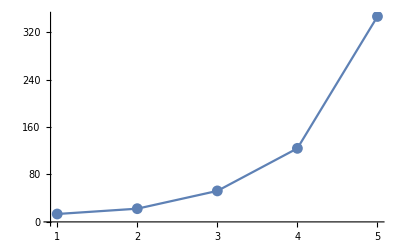

```mathematica
ListLinePlot[#,Mesh->All,PlotRange->All]&@%
```

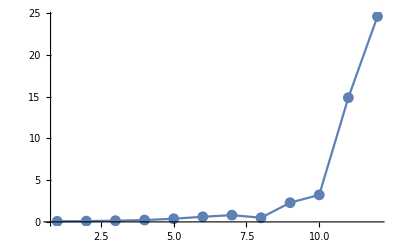

```mathematica
ListLinePlot[{0.072022,0.093026,0.143084,0.219773,0.380295,0.613662,0.811804,0.497553,2.300937,3.239144,14.890997,24.627013},Mesh->All,PlotRange->All]
```

```mathematica
ZAnd[jt10≥0&&0≤jt11≤104&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥208+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000≤364+8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤-3328-44 jt10+43 jt17+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-1000≤3276+52 jt10-49 jt17-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&364+4 jt10+jt27+jt28≥4 jt17+4 jt18+jt41+jt42&&jt17+jt18≤52+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&208+3 jt10+jt19≤4 jt17+3 jt18+jt22&&208+3 jt10+jt28≤4 jt17+3 jt18+jt22&&364+4 jt10+jt16+jt28≥5 jt17+4 jt18+jt22&&156+jt10+jt16≥jt17+jt18&&780+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (1170+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&780+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥1560+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48,sorted]//AbsoluteTiming
```

```mathematica
Length[Last[%]]
Length[Simplify/@Last[%%]]
```

ZAnd: head is and: jt17==0||jt19==0

ReZAnd: jt17==0 (jt10==jt19||jt18==0)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==jt19||jt18==0

ReZAnd: jt10==jt19 (jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt29==0||jt32==0

ReZAnd: jt29==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt32==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt18==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt18==0

ReZAnd: jt18==0 (jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt29==0||jt32==0

ReZAnd: jt29==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt32==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 jt10==0||jt11==-jt16

ReZAnd: jt48==0 jt10==0||jt11==-jt16

ReZAnd: jt19==0 (jt10==0||jt18==0)&&(jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==-jt18)

ZAnd: head is and: jt10==0||jt18==0

ReZAnd: jt10==0 (jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt29==0||jt32==0

ReZAnd: jt29==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 jt45==0||jt48==0

ReZAnd: jt47==0 jt45==0||jt48==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 jt45==0||jt48==0

ReZAnd: jt47==0 jt45==0||jt48==0

ReZAnd: jt32==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 jt45==0||jt48==0

ReZAnd: jt47==0 jt45==0||jt48==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 jt45==0||jt48==0

ReZAnd: jt47==0 jt45==0||jt48==0

ReZAnd: jt18==0 (jt29==0||jt32==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt29==0||jt32==0

ReZAnd: jt29==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt32==0 (jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt41==0||jt44==0

ReZAnd: jt41==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt44==0 (jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt42==0||jt47==0

ReZAnd: jt42==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt47==0 (jt45==0||jt48==0)&&(jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt45==0||jt48==0

ReZAnd: jt45==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

ReZAnd: jt48==0 (jt10==0||jt11==-jt16)&&(jt10==0||jt17==0)

ZAnd: head is and: jt10==0||jt11==-jt16

ReZAnd: jt10==0 True

ReZAnd: jt11==-jt16 jt10==0||jt17==0

{0.620194,1}
 |  |  |  |

128

128

```mathematica
Length[Simplify/@Last[%28]]
```

8

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

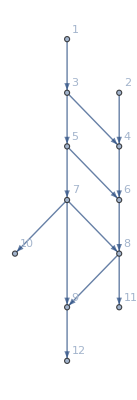

```mathematica
d2e["jtvars"]
d2e["BG"]
```

```mathematica
crit[d2e["jvars"][{5,3->5}]]
crit[d2e["jvars"][{6,4->6}]]
crit[d2e["jvars"][{7,5->7}]]
crit[d2e["jvars"][{8,6->8}]]
crit[d2e["jvars"][{11,8->11}]]
crit[d2e["jvars"][{10,7->10}]]
crit[d2e["jvars"][{7,7->8}]]
crit[d2e["jvars"][{8,7->8}]]
crit[d2e["jvars"][{12,9->12}]]
crit[d2e["jvars"][{5,3->5}]]
```

71

85

76

80

59

58

jt33+jt34

-1+jt33+jt34

39

71

```mathematica
crit[d2e["jvars"][{11,8->11}]]+crit[d2e["jvars"][{10,7->10}]]+crit[d2e["jvars"][{12,9->12}]]
```

156

```mathematica
sys=
vars=Select[FixedPoint[Flatten[List @@@#]& ,List @@ sys]//DeleteDuplicates, Not[NumberQ[#]]&];
FindInstance[sys,vars,Reals]
```

{{jt30→0,jt33→1/26,jt34→7/52}}

```mathematica
Reduce[sys,Reals]
```

(jt34==7/52&&jt30==0&&jt33==1/26)||(7/52<jt34<9/52&&jt30==1/52 (-7+52 jt34)&&jt33==1/26 (1-26 jt30))||(jt34==9/52&&jt30==1/26&&jt33==0)

```mathematica
FindInstance[(7/52<jt34<9/52&&jt30==1/52 (-7+52 jt34)&&jt33==1/26 (1-26 jt30)),vars,Reals]
```

{{jt30→1371/136604,jt33→3883/136604,jt34→380/2627}}

```mathematica
Variables[List@@List@@@sys//Flatten]
```

{}

```mathematica
NonLinear[d2e];
```

```mathematica
{KK,BB,cost,vars}=GetKirchhoffMatrix[d2e]
```

{SparseArray[…],SparseArray[…],Function[currents$,MapThread[#1[#2]&,{KeyMap[Join[jvars$5488229,jtvars$5488229]][CostArgs$5488229]/@vars$5488229,currents$}]],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}

```mathematica
cost[vars]
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,0,0,0,0,0,j4,j5,j6,j7,j8,j9,100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100,1/100,100,1/100,100,1/100,1/100,1/100}

```mathematica
D[cost[vars],vars]
```

D::dvar: Multiple derivative specifier {j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,«87»} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9} {j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,0,0,0,0,0,j4,j5,j6,j7,j8,j9,100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,1/100,100,1/100,100,1/100,100,1/100,1/100,1/100}

#### Non-linear case

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

# kdkd

```mathematica
(*Wolfram Language package*)D2E::usage="D2E[<|\"Vertices List\" -> {1, 2, 3}, \"Adjacency Matrix\" -> {{0, 0, 0}, {1, 0, 1}, {0, 0, 0}}, 
 \"Entrance Vertices and Currents\" -> {{2, I1}}, 
 \"Exit Vertices and Terminal Costs\" -> {{1, U1}, {3, U2}}, 
 \"Switching Costs\" -> {{1, 2, 3, S1}, {3, 2, 1, S2}}|> returns the equations for the stationary mean-field game on the network.]"

Begin["`Private`"]
D2E[Data_Association]:=Module[{BG,FG,AuxiliaryGraph,VL,FVL,EntranceVertices,InwardVertices,ExitVertices,OutwardVertices,EL,BEL,OutEdges,InEdges,ExitNeighbors,AllTransitions,EqCcs,SC=Lookup[Data,"Switching Costs",{}],jargs,js,jvars,jts,jtvars,uargs,us,uvars,SignedCurrents,EntryArgs,NoDeadEnds,NoDeadStarts,ExitCosts,EntryDataAssociation,SwitchingCosts,EqPosCon,EqCurrentCompCon,EqTransitionCompCon,EqSwitchingByVertex,EqSwitchingConditions,EqCompCon,EqValueAuxiliaryEdges,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,Nrhs,Nlhs,MinimalTimeRhs,AllOr,EqAllAll,AllIneq,EqCriticalCase,EqMinimalTime,EqNonCritical,EqPosJs,TrueEq,costpluscurrents,RuleBalanceGatheringCurrents,RuleEntryIn,RuleEntryOut,RuleExitValues,RuleExitCurrentsIn,InitRules,OutRules,InRules,RuleNonCritical,RuleNonCritical1,RulesCriticalCase,RulesCriticalCase1,(*,EqNonCritical1*)EqPosJts,BalanceSplittingCurrents,BalanceGatheringCurrents,EqEntryIn,Kirchhoff,RuleValueAuxiliaryEdges,BM,KM,vars},(*Checking consistency on the swithing costs*)If[SC=!={},ConsistentSwithingCosts[sc_][{a_,b_,c_,S_}]:=Module[{or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];
EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: \n",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
(****Graph stuff****)BG=AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name",DirectedEdges->True];
EntranceVertices=First/@Data["Entrance Vertices and Currents"];
ExitVertices=First/@Data["Exit Vertices and Terminal Costs"];
Clear["en*"];
(*InwardVertices defines auxiliary vertices for the entrance vertices*)InwardVertices=AssociationThread[EntranceVertices,Symbol["en"<>ToString[#]]&/@EntranceVertices];
Clear["ex*"];
OutwardVertices=AssociationThread[ExitVertices,Symbol["ex"<>ToString[#]]&/@ExitVertices];
(*InEdges defines auxiliary arguments for the entrance vertices*)InEdges=MapThread[DirectedEdge,{InwardVertices/@EntranceVertices,EntranceVertices}];
OutEdges=MapThread[DirectedEdge,{ExitVertices,OutwardVertices/@ExitVertices}];
AuxiliaryGraph=Graph[Join[InEdges,OutEdges],VertexLabels->"Name",GraphLayout->"SpringEmbedding"];
FG=EdgeAdd[BG,Join[InEdges,OutEdges]];
VL=Data["Vertices List"];
EL=EdgeList[FG];
BEL=EdgeList[BG];
FVL=VertexList[FG];
(*arguments*)jargs=Flatten[#,1]&@({AtTail@#,AtHead@#}&/@EL);
uargs=jargs;
AllTransitions=TransitionsAt[FG,#]&/@FVL//Catenate(*at vertex from first edge to second edge*);
EntryArgs=AtHead/@((EdgeList[AuxiliaryGraph,_->#]&/@(First/@Data["Entrance Vertices and Currents"]))//Flatten[#,1]&);
EntryDataAssociation=RoundValues@AssociationThread[EntryArgs,Last/@Data["Entrance Vertices and Currents"]];
ExitCosts=AssociationThread[OutwardVertices/@(First/@Data["Exit Vertices and Terminal Costs"]),Last/@Data["Exit Vertices and Terminal Costs"]];
(*variables*)js=Table[Symbol["j"<>ToString[k]],{k,1,Length@jargs}];
jvars=AssociationThread[jargs,js];
jts=Table[Symbol["jt"<>ToString[k]],{k,1,Length@AllTransitions}];
jtvars=AssociationThread[AllTransitions,jts];
us=Table[Symbol["u"<>ToString[k]],{k,1,Length@uargs}];
uvars=AssociationThread[uargs,us];
costpluscurrents=Table[Symbol["cpc"<>ToString[k]],{k,1,Length@BEL}];
(*costpluscurrentsvars=AssociationThread[BEL,costpluscurrents];*)SignedCurrents=AssociationThread[BEL,(jvars[AtHead[#]]-jvars[AtTail[#]]&)/@BEL];
Print["D2E: Variables are all set"];
(*Elements of the system*)(*Swithing cost is initialized with 0. AssociationThread associates the last association!*)SwitchingCosts=AssociationThread[Join[AllTransitions,triple2path[Take[#,3],FG]&/@SC],Join[0&/@AllTransitions,Last[#]&/@SC]];
SC=path2triple/@Normal[SwitchingCosts];
If[SC=!={},Print["Second check:"];
(*ConsistentSwithingCosts[{a_,b_,c_,S_}]:=Module[{sc=SC,or,de,bounds},or=Cases[sc,{a,b,_,_}];
de=Cases[sc,{_,b,c,_}];
bounds=Outer[Plus,Last/@or,Last/@de]//Flatten;
(*And@@(NonNegative[#-S]&)/@bounds*)And@@(#>=S&)/@bounds];*)EqCcs=ConsistentSwithingCosts[SC]/@SC;
EqCcs=Simplify[EqCcs];
(*Print[EqCcs];*)If[AnyTrue[EqCcs,#===False&],Print["DataToEquations: Triangle inequalities for switching costs: ",Select[AssociationThread[SC,EqCcs],Function[exp,!TrueQ[exp]]]];
Print["DataToEquations: The switching costs are ",Style["incompatible",Red],". \nStopping!"];
Return[]]];
EqPosJs=And@@(#>=0&/@Join[jvars]);(*Inequality*)EqPosJts=And@@(#>=0&/@Join[jtvars]);(*Inequality*)EqPosCon=EqPosJs&&EqPosJts;(*Inequality*)EqCurrentCompCon=And@@(CurrentCompCon[jvars]/@EL);(*Or*)EqTransitionCompCon=And@@((Sort/@TransitionCompCon[jtvars]/@AllTransitions)//Union);(*Or*)(*Balance Splitting Currents in the full graph*)NoDeadEnds=IncomingEdges[FG]/@VL//Flatten[#,1]&;
EqBalanceSplittingCurrents=And@@((jvars[#]==Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);(*Equal*)BalanceSplittingCurrents=((jvars[#]-Total[jtvars/@CurrentSplitting[AllTransitions][#]])&/@NoDeadEnds);
(*Gathering currents in the inside of the basic graph*)NoDeadStarts=OutgoingEdges[FG]/@VL//Flatten[#,1]&;
RuleBalanceGatheringCurrents=(jvars[#]->Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts;(*Rule*)(*First rules:these have some j in terms of jts*)InitRules=Association[RuleBalanceGatheringCurrents];
(*get equations for the exit currents at the entry vertices*)BalanceGatheringCurrents=((-jvars[#]+Total[jtvars/@CurrentGathering[AllTransitions][#]])&/@NoDeadStarts);
EqBalanceGatheringCurrents=Simplify/@(And@@(#==0&/@BalanceGatheringCurrents));
(*Incoming currents*)EqEntryIn=(jvars[#]==EntryDataAssociation[#])&/@(AtHead/@InEdges);(*List of Equals*)RuleEntryIn=Flatten[ToRules/@EqEntryIn];(*List of Rules*)Kirchhoff=Join[EqEntryIn,(#==0&/@(BalanceGatheringCurrents+BalanceSplittingCurrents))];
(*Print["The matrices B and K are: \n",MatrixForm/@CoefficientArrays[Kirchhoff,vars=RandomSample@Join[js,jts]],"\nThe order of the variables is \n",vars];*)(*Outgoing currents at entrances*)RuleEntryOut=(jvars[#]->0)&/@(AtTail/@InEdges);(*Rule*)RuleEntryIn=Join[RuleEntryIn,RuleEntryOut];
(*Not necessary to replace RuleEntryIn in InitRules*)AssociateTo[InitRules,RuleEntryIn];
(*Include Gathering currents information in the rules*){TrueEq,InitRules}=CleanEqualities[{EqBalanceGatheringCurrents/. RuleBalanceGatheringCurrents,InitRules}];
ExitNeighbors=IncidenceList[AuxiliaryGraph,OutwardVertices/@ExitVertices];
Print[ExitNeighbors];
Print[OutEdges];
(*TODO this seems to be defined already:OutEdges*)(*Incoming currents at the exits are zero*)RuleExitCurrentsIn=ExitCurrents[jvars]/@ExitNeighbors;(*Rule*)Kirchhoff=Kirchhoff/. Join[RuleExitCurrentsIn,RuleEntryOut];
{BM,KM}=CoefficientArrays[Kirchhoff,vars=Variables[Kirchhoff/. Equal->Plus]];
Print["The matrices B and K are: \n",MatrixForm/@{-BM,KM},"\nThe order of the variables is \n",vars];
AssociateTo[InitRules,RuleExitCurrentsIn];
(*Exit values at exit vertices*)RuleExitValues=ExitRules[uvars,ExitCosts]/@ExitNeighbors;(*Rule*)(*Not necessary to replace RuleExitValues in InitRules,there are no us up to now.*)Print[RuleExitValues];
AssociateTo[InitRules,RuleExitValues];
(*The value function on the auxiliary edges is constant and equal to the exit cost.*)EqValueAuxiliaryEdges=And@@((uvars[AtHead[#]]==uvars[AtTail[#]])&/@Join[InEdges,OutEdges]);(*Equal*)RuleValueAuxiliaryEdges=(uvars[AtTail[#]]->uvars[AtHead[#]])&/@Join[InEdges,OutEdges];(*Equal*)Print["D2E: CleanEqualities for the values at the auxiliary edges"];
{TrueEq,InitRules}=CleanEqualities[{EqValueAuxiliaryEdges,InitRules}];
(*Print[RuleValueAuxiliaryEdges];*)(*Infinite switching costs here prevent the network from sucking agents from the exits.*)OutRules=Rule[#,Infinity]&/@(Outer[Flatten[{AtTail[#1],#2}]&,OutEdges,EL]//Flatten[#,1]&);
InRules=Rule[#,Infinity]&/@(Outer[{#2[[2]],#1,#2}&,IncidenceList[FG,#]&/@EntranceVertices,InEdges]//Flatten[#,2]&);
AssociateTo[SwitchingCosts,Association[OutRules]];
AssociateTo[SwitchingCosts,Association[InRules]];
Print["D2E: Assembled most elements of the system"];
(*Switching condition equations*)EqSwitchingByVertex=Transu[uvars,SwitchingCosts]/@TransitionsAt[FG,#]&/@VL;
(*EqSwitchingByVertex=BooleanConvert[Reduce[Reduce@#,Reals],"CNF"]&/@EqSwitchingByVertex;*)(*Maybe this is good with nonzeroswitching costs.*)EqSwitchingByVertex=BooleanConvert[Reduce[#,Reals],"CNF"]&/@EqSwitchingByVertex;
EqSwitchingByVertex=DeleteCases[EqSwitchingByVertex,True];
Print["D2E: CleanEqualities for the switching conditions on each vertex: \n",Reduce@EqSwitchingByVertex];
{EqSwitchingConditions,InitRules}=CleanEqualities[{EqSwitchingByVertex,InitRules}];
EqCompCon=And@@Compu[jtvars,uvars,SwitchingCosts]/@AllTransitions;(*Or*)Print["D2E: CleanEqualities for the complementary conditions (given the rules)"];
{EqCompCon,InitRules}=CleanEqualities[{EqCompCon,InitRules}];
(*Default in a,function,corresponds to the classic critical congestion case*)a (*[SignedCurrents[edge],edge]:*)=Lookup[Data,"a",Function[{j,edge},j]];
MinimalTimeRhs=Flatten[-a[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];
Nlhs=Flatten[uvars[AtHead[#]]-uvars[AtTail[#]]+SignedCurrents[#]&/@BEL];
EqMinimalTime=And@@(MapThread[(#1==#2)&,{Nlhs,MinimalTimeRhs}]);
Nrhs=Flatten[-Cost[SignedCurrents[#],#]+SignedCurrents[#]&/@BEL];(*one possible cost is IntM*)Print["D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents"];
{TrueEq,InitRules}=CleanEqualities[{EqBalanceSplittingCurrents,InitRules}];
AllOr=EqCurrentCompCon&&EqTransitionCompCon&&EqCompCon;
AllOr=AllOr/.InitRules;
AllOr=BooleanConvert[Simplify/@AllOr,"CNF"];
{AllOr,InitRules}=CleanEqualities[{AllOr,InitRules}];
EqPosCon=EqPosCon/. InitRules;
EqSwitchingConditions=EqSwitchingConditions/.InitRules;
EqSwitchingConditions=Simplify[EqSwitchingConditions];
AllOr=AllOr&&Select[EqSwitchingConditions,Head[#]===Or&];
AllOr=BooleanConvert[AllOr,"CNF"];
AllIneq=EqPosCon&&Select[EqSwitchingConditions,Head[#]=!=Or&];
AllIneq=Simplify[AllIneq];
(*AllOr=BooleanConvert[Simplify[#,AllIneq]&/@AllOr,"CNF"];
{EqAllAll,InitRules}=CleanEqualities[{AllOr&&AllIneq,InitRules}];*)EqCriticalCase=And@@((#==0)&/@Nlhs);(*Equal*)EqNonCritical=And@@(MapThread[Equal[#1,#2]&,{Nlhs,costpluscurrents/.InitRules}])/.AssociationThread[us,us/.InitRules];
RuleNonCritical1=Solve[EqNonCritical,Reals]//Quiet;
(*The operations below are commutative! Print[RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print[Solve[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents],Reals]//Quiet];*)(*Print[EqCriticalCase/.AssociationThread[us,us/.InitRules]];
Print[EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]];
Print["right?\n",(EqCriticalCase/.AssociationThread[us,us/.InitRules])/.RuleNonCritical1];
Print["right?\n",(EqCriticalCase/. AssociationThread[costpluscurrents,0&/@costpluscurrents])/.(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents])];
Print[EqNonCritical/. RuleNonCritical1];*)Print["D2E: CleanEqualities for the (non) critical case equations"];
{TrueEq,RuleNonCritical}=CleanEqualities[{EqNonCritical,InitRules}];
(*Print[Expand/@RuleNonCritical];*)EqCriticalCase=EqNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents];
(*Print[EqCriticalCase];*)RulesCriticalCase1=Expand/@(RuleNonCritical1/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
RulesCriticalCase=Expand/@(RuleNonCritical/. AssociationThread[costpluscurrents,0&/@costpluscurrents]);
(*Here we change the pourpose of costpluscurrents*)costpluscurrents=AssociationThread[costpluscurrents,Nrhs];
(*Print[Solve[EqCriticalCase,js]];
(*RulesCriticalCaseJs=Association@First[Solve[EqCriticalCase/.RuleEntryIn,js]];*)Print["CleanEqualities for the critical case equations"];
{TrueEq,RulesCriticalCase}=CleanEqualities[{EqCriticalCase,InitRules}];
Print["Expanding critical rules..."];
RulesCriticalCase=Expand/@RulesCriticalCase;
Print[RulesCriticalCase];*)Print["D2E: D2E is finished!"];
Print[$Context];
Print[Names[$Context<>"*"]];
ttt=1;
Print[Names[$Context<>"*"]];
Join[Data,Association[(*Graph structure*)"BG"->BG,"InEdges"->InEdges,"OutEdges"->OutEdges,"FG"->FG,(*variables*)"jvars"->jvars,"jtvars"->jtvars,"uvars"->uvars,"costpluscurrents"->costpluscurrents,"jays"->SignedCurrents,(*equations*)(*complementarity*)"AllOr"->AllOr,(*union of all complementarity conditions*)"AllIneq"->AllIneq,"EqPosJs"->EqPosJs,"EqPosJts"->EqPosJts,"EqPosCon"->EqPosCon,"EqCurrentCompCon"->EqCurrentCompCon,"EqTransitionCompCon"->EqTransitionCompCon,(*linear equations (and inequalities)*)"EqAllAll"->EqAllAll,"BoundaryRules"->InitRules,"InitRules"->InitRules,"RulesCriticalCase"->RulesCriticalCase,"RulesCriticalCase1"->RulesCriticalCase1,(*"RulesCriticalCaseJs"->RulesCriticalCaseJs,*)"RuleExitValues"->RuleExitValues,"RuleEntryIn"->RuleEntryIn,"Nlhs"->Nlhs,"MinimalTimeRhs"->MinimalTimeRhs,"EqCriticalCase"->EqCriticalCase,"EqNonCritical"->EqNonCritical,(*"EqNonCritical1"->EqNonCritical1,*)"RuleNonCritical"->RuleNonCritical,"RuleNonCritical1"->RuleNonCritical1,"EqSwitchingConditions"->And@@EqSwitchingByVertex,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"EqBalanceSplittingCurrents"->EqBalanceSplittingCurrents,"EqBalanceGatheringCurrents"->EqBalanceGatheringCurrents,"Nrhs"->Nrhs,"B"->BM,"K"->KM,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,"EqEntryIn"->EqEntryIn,"vars"->vars]]]


(*"EntranceVertices"->EntranceVertices,*)
(*"InwardVertices"->InwardVertices,*)
(*"ExitVertices"->ExitVertices,*)
(*"OutwardVertices"->OutwardVertices,*)
(*"AuxiliaryGraph"->AuxiliaryGraph,*)
(*"VL"->VL,"EL"->EL,"BEL"->BEL,"FVL"->FVL,*)
(*"AllTransitions"->AllTransitions,"NoDeadEnds"->NoDeadEnds,"NoDeadStarts"->NoDeadStarts,*)
(*"jargs"->jargs,"js"->js,*)
(*"jts"->jts,*)
(*"uargs"->uargs,"us"->us,*)
(*"SwitchingCosts"->SwitchingCosts,*)
(*"OutRules"->OutRules,*)
(*"InRules"->InRules,*)
(*"EntryArgs"->EntryArgs,*)
(*"EntryDataAssociation"->EntryDataAssociation,*)
(*"ExitCosts"->ExitCosts,*)
(*"EqCompCon"->EqCompCon,*)
(*"EqPosCon"->EqPosCon,"EqEntryIn"->EqEntryIn,"EqExitValues"->EqExitValues,"EqValueAuxiliaryEdges"->EqValueAuxiliaryEdges,"AllIneq"->AllIneq,*)



End[]
```